```mathematica
<<KnotTheory`
```

Loading KnotTheory` version of March 22, 2011, 21:10:4.67737.
Read more at http://katlas.org/wiki/KnotTheory.

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Changes 6_8_12

#### changes to code

1.updated computation for writhe, acn (faster) and curvature and torsion (corrected)
2. updated version of initPolyGeneration  to account for more volumefiles with differnt naming schemes
3. added functions to compute the breadth of the jones polynomial and a function to compute the knot (if it’s in the table) or the lower
bound on the cr (function: crorlookuppd[pd_, timeconstraint_]
4. added/updated functions to compute the volume functions in two steps: first all the integrals which are the same, and secondly the last integra.

## Changes 11_9_11

#### changes to code

1. Modified initPolyGeneration to load for steps > 20; note that the volumne functions are expected to be in a certain subdirectory 
2. Modified findrad to no longer have two cases (t+1 > ra and t+r <= R)

## Changes 10_6_11

#### changes to code

1. Added function cdvalforceConfine and cdvalforceConfineClose to compute the new cdf - has parameters steps, tau, R, and p
2. Added function cdfvalshortNoDenom computing H without the denominator
3. Modified findrad function to compute full probability value for new approach and to use cdvalforceConfine or cdvalforceConfineClose (whichever is needed)
4. Old findrad function is now called fineradfast. Removed limitation on 50 iterations in the loop of findrad.
5. Commented out determineR function since we currently don’t have a accept/reject approach and added determineR function without it. 
6. Added volume function - modified to use k instead of k+1
7. Added initPolyGeneration function to load in the functions needed for the generation
8. Change generateConfinedPoly and determinR to use exact tau

## Changes 9_18.5_11

#### changes to code

1.  Edited DT connected sum parser to remove unknots (knots with less than 3 crossings) detected as part of the prime decomposition. Prime components do not allow for R1 or R2 moves anymore. 
2. Allowed non-integer values for the confinement radius for generatefixedoffsetfilebatch and generatefixedoffsetfilebatchstartstop. Filenames now include “Rnumerator_denominator” of the exact fraction for the confinement radius. For R = 1.5, the filename contains R3_2.

## Changes 9_18_11

#### changes to code

1.  Edited PD connected sum parser to reduce the types of unknots detected as prime components
2.  Excluded NotebookDirectory[] concatenation from file commands and instead by default sets directory at beginning of file. The limitation of this is that now by default any notebook needing the functions in this toolkit will create files in the toolkit directory instead of the directory of the notebook calling the functions. Easily changed by setting the directory in the calling notebook.
5. Added a rotator error example. The rotator seems to malfunction on lattice or near lattice polygons. 
SAVE YOUR WORK BEFORE EXECUTING THIS EXAMPLE!

## Changes 9_14_11

#### changes to code

1. Fixed the PolyinSphere function

Added more documentation to the Knotfinder, File convention, testpolygon sections

## Changes 9_12_11

#### changes to code

1. Expanded/Debugged Planar Diagram functions
	- if we find a segment intersection the code calls Abort[ ];
	- R1,R2,R3 moves are now reduced consistently and without errors
	- connected sums can be parsed with decomposePD[ pdcode ];
	- transformation functions added to go back and forth from list representation of the pd code and the 	KnotTheory package's PD[ X[ ...], ... ] representation (mappd [ listpd] , unmappd[ PD ] )
	- preliminary PD to polygon function added polygonFromPD[listpd] this polygon is reversed to compensate for error in morselink conversion
	- added abbreviation command to draw pd codes with drawpd[listpd], this uses drawmorselink which seems more stable and faster than DrawPD but may give the mirror image of the knot intended
2. Fixed reducer to allow full reduction at every step (not previously/necessarily implemented). Set default safety value to zero.
3. Added knotatlas' code for knot lookup i.e., IdentifyWithin[ PDcode , AllKnots[ ] ];
4. Moved KnotTheory` import to beginning of file to prevent possible shadowing issues.

## Changes 9_11_11

#### changes to code

1. Corrected dowker code comands decomposedt to work correctly with negatives.
2. Added meanpathdist function
3. Added radius of gyration radgyr[lst_]

#### Added section Documentation, Limitations and Examples

#### Add display function of polygon in sphere

## Documentation, Limitations and Examples

### File conventions

If there is a file to be read in, put it in the same directory as the RandomPolygonToolkit file. The output will also be written to a file that is in the same directory as the RandomPolygonToolkit file. The only exception is the allcalc[..] functions in the path calculation section.

In order to use these functions do the following

a. Create three directory (folders) called data, flags and polygons which sit in a common parent directory (folder). 
b. Put the file RandomPolygonToolkit.nb in the directory (folder) polygons. 
c. Any files containing the polygondata have to be also in the polygons directory (folder).
d. The dataoutput created will be located in the two directories (folders) data and flags. The directory (folder) data contains the files with the output data. The directory (folder) flags will contain the files containing the flags. The flags only indicate problems with the computations and if there are only a small number of flags then they may be ingnored.

### testpolygons

an unknot

```mathematica
testpoly={{0,0,0},{0.2027316099671975,-0.2905715029254452,0.9351299888292302},{-0.5616704411469235,0.3345915136954332,1.0928027731073293},{0.22232405112195353,0.9428118334802961,0.9686227477696574},{-0.5533803180081543,1.00416279291412,0.3405154388733104},{-0.18894837887233992,0.14064716965803237,0.6891271571651092},{0.4635916034092878,0.5626995549337546,0.05979151094207398},{0.728278068249634,0.3198973531255371,0.9930589785671926},{0.3391081312164841,0.42431717250820095,0.07783044894756477},{-0.09633689457309336,1.3190348940667622,-0.02150649405034974},{0.6140716947925511,0.8940766705207293,-0.5825146440768137},{-0.10432738519687473,0.2588412137379732,-0.8660259777415362},{-0.6176062596953688,-0.5110123123294431,-0.48672353193459855},{-0.76009058655302,-0.16826973175714507,0.4418375807890409},{-1.3333030869235176,0.4638090457744234,-0.07960642235338677},{-0.7063333316306877,0.321441236742225,0.6863180732069919},{-0.12723721017122647,0.06818818456746756,1.461244246254966},{-0.04596036464780813,-0.8790993312549511,1.151340330905784},{-0.7365552101881101,-1.052115223634055,0.4490980220853672},{-0.9444643085456277,-0.08279030451750868,0.31801404899992586},{0,0,0}};
```

```mathematica
Graphics3D[prettyReturn[testpoly,.1]]
```

-Graphics3D-

This is the knot 7_1as a minimal stick knot

```mathematica
stick9knot71={{-14.1290948304074657216,-22.6496315733981390395,-18.0558960444480689489},
{-13.7496054174481621146,9.4073491057062170739,8.4017284004146226550},{
14.8376842875557279910,-17.9742172573713787642,-4.2796099290585054575},{
3.7199907329964867486,20.4478738723734103644,7.0314264592100705897},{
-3.7190658714125395257,-20.4478530889670295778,7.0318836941504487825},{
-14.8381986768636551233,17.9741860822618058080,-4.2779264731416581924},{
13.7505302790321088935,-9.4074166517769537421,8.4001072947169159733},{
14.1269229644406681956,22.6498757784231159462,-18.0571846156436777164},{
0.0008365321068287003,-0.0001714631026419100,13.8054712137998532029},{-14.1290948304074657216,-22.6496315733981390395,-18.0558960444480689489}};
```

```mathematica
Graphics3D[prettyReturn[stick9knot71,.2]]
```

-Graphics3D-

This is a lattice representatin of 8_2

```mathematica
lattice82knot={{2,4,1},{2,3,1},{2,2,1},{2,1,1},{2,0,1},{2,0,2},{2,0,3},{2,1,3},{2,2,3},{3,2,3},{4,2,3},{4,3,3},{4,4,3},{4,4,2},{3,4,2},{2,4,2},{1,4,2},{0,4,2},{0,3,2},{0,2,2},{1,2,2},{2,2,2},{3,2,2},{3,2,1},{3,2,0},{2,2,0},{1,2,0},{1,1,0},{1,1,1},{1,1,2},{2,1,2},{3,1,2},{3,1,3},{3,1,4},{3,2,4},{3,3,4},{3,3,3},{3,3,2},{3,3,1},{3,3,0},{2,3,0},{1,3,0},{1,3,1},{1,3,2},{1,3,3},{1,4,3},{1,5,3},{2,5,3},{2,5,2},{2,5,1},{2,4,1}};
```

```mathematica
Graphics3D[prettyReturn[lattice82knot,.2]]
```

-Graphics3D-

### Random Polygon Generation

generateConfinedPolygon[steps_,centerZValue_, confinementRadius_,acc_]
This generates a polygon confined in a sphere of radius confinementRadius.
steps is the length of the polygon
acc is the accuracy given as a number in the form 10^-d for d digits of accuracy.
centerZValue is the offest of the starting point of the polygon from the center of the sphere.

Method: If there are less or equal 20 remaining or τ_k >5 then we use the accept/reject method, otherwise we use the “inverse lookup” for the exact cdf.

```mathematica
v=generateConfinedPolygon[30,0.7,1,10^-10]
PolyinSphere[v,.02,1,0.7]
```

{{0,0,0},{-0.101378,0.6309,0.769212},{-0.150654,-0.275862,1.18796},{0.288619,-0.83893,0.487967},{-0.563872,-0.32981,0.369404},{0.0168365,0.0824592,1.07141},{-0.563065,-0.690269,0.813329},{0.403487,-0.584498,1.04697},{0.198423,0.0533859,0.304645},{0.0351425,-0.595049,1.0482},{-0.312699,-0.0515306,0.284265},{-0.138129,0.41092,1.15356},{0.72721,-0.0877064,1.10295},{0.0647605,-0.808217,0.897951},{0.0488114,-0.435512,-0.0298618},{0.167518,0.512052,0.266838},{-0.483498,0.776219,0.978452},{-0.97378,-0.0407807,0.674915},{-0.30952,-0.684293,0.294585},{-0.635961,0.256204,0.200243},{0.354196,0.266487,0.339825},{-0.61397,0.247264,0.589391},{0.0706913,0.026253,-0.105153},{0.79097,0.351235,0.507696},{0.65774,-0.355299,1.20272},{0.163958,0.428878,0.826895},{-0.704359,0.244734,1.28746},{-0.0842671,-0.340559,0.765041},{0.0025747,0.494582,1.30818},{-0.481961,-0.245123,0.841207},{0,0,0}}

-Graphics3D-

### Rotator

1. rotator[pList_,n_] 
This performs “n” rotations of random degree on random vertices of the polygon specified by the list of points “pList” 
Limitations: 

2. rotatorF[pList_,n_] 
This performs “n” rotations of random degree on random vertices of the polygon specified by the list of points “pList” ignoring selfintersections, thus this changes the knot type.
Limitations:

```mathematica
newtestpoly=rotator[testpoly,100];
GraphicsGrid[{{Graphics3D[prettyReturn[testpoly,.1]],Graphics3D[prettyReturn[newtestpoly,.1]]}}]
```

-Graphics-

```mathematica
newlattice82knot=rotator[lattice82knot,100];
GraphicsGrid[
{{Graphics3D[prettyReturn[lattice82knot,.1]],Graphics3D[prettyReturn[newlattice82knot,.1]]}}]
```

Power::infy: Infinite expression 1/0 encountered.

∞::indet: Indeterminate expression 0 ComplexInfinity encountered.

LinearFractionalTransform::inpf: {« 1 »} is not a matrix or a list containing a matrix, two vectors, and a scalar.

Part::partw: Part 30 of TransformationFunction[(TagBox[GridBox[{{ does not exist.

RotateLeft::normal: Nonatomic expression expected at position 1 in RotateLeft[4].

```mathematica
newtestpoly=rotatorF[testpoly,100];
GraphicsGrid[{{Graphics3D[prettyReturn[testpoly,.1]],Graphics3D[prettyReturn[newtestpoly,.1]]}}]
```

-Graphics-

### Reducer

1. reduce[lst_]
This function tries to reduce a polygon by picking a random vertex v.  v and its two neighbors x and y form a triangle. If no other edges of the polygon intersect the triangle xyv then the edges xv and yv can be replaced by a single egde xy. If there is an intersection then it might be possible to make the edges xv and yv shorter. 

The code works as follows

if fullReduce=False:
	a) each iteration we cycle through all vertices in a random order
	b) for each vertex randomly decide if we want to attempt to remove the vertex
	c) if yes : if we can we do if we can't we skip said vertex
	    if no : randomly pick an amount to reduce between 0.2 and 0.8 of complete colinearity and see if such a 		reduction is possible
	d) if the number of vertices isn't lowered for 8 consecutive iterations or the segment number drops below 6 		we stop and return
if fullReduce=True same except change the c) if no : reduce to 0.9 of the maximum possible move towards colinearity
	    
Limitations:
Repeated use of the reudce can create polygon that are extremly tight with almost intersection.

2. ReduceFile[name_]
Same as reduce except assumes the polygon resides in a file

```mathematica
newtestpoly=reduce[testpoly];
newtestpoly2=reduce[reduce[testpoly]];
GraphicsGrid[{{Graphics3D[prettyReturn[testpoly,.1]],Graphics3D[prettyReturn[newtestpoly,.1]],Graphics3D[prettyReturn[newtestpoly2,.1]]}}]
```

-Graphics-

### Path Calculations

1. acn[lst_] calculates the acn of a polygon using the projection into the x-y plane based on the Gauss integral formula.
Limitations: Problems are very likely if there are very tight almost intersections.
Returns: {a,b,c,d,e}
a = acn computed
b = acn computed where in the sum the the cases where convergence gives problems are omitted
c,d and e are flags indicating various problems
c = the number of times the integral did not converge that is even after increase in presicion NIntegrate still gives a warning about convergence
d = minimum value of the acn of a pair of edges where slow convergence happened (the default value of this is one)
e= the number of times happens the acn of a pair of edges was greater than one, default is zero.

2. wri[lst_] calculates the acn of a polygon using the projection into the x-y plane based on the Gauss integral formula.
Limitations: Problems could arise if there are very tight almost intersections.
Returns: {a,b,c,d,e}
a = acn computed
b = acn computed where in the sum the the cases where convergence gives problems are omitted
c,d and e are flags indicating various problems
c = the number of times the integral did not converge that is even after increase in presicion NIntegrate still gives a warning about convergence
d = minimum value of the acn of a pair of edges where slow convergence happened (the default value of this is one)
e= the number of times happens the acn of a pair of edges was greater than one, default is zero.

3. curv[lst_] returns the total curvature of a polygon
Limitations: None

4. tors[lst_] returns the total torsion of a polygon
Limitations: None

5. pathDist[lst_] returns the spacial distance from v_1 to v_mid of a polygon where the middle is the floor of the length/2 

6. meanpathDist[lst_] returns the spacial distance from v_i to v_(i+mid) of a polygon where the middle is the floor of the length/2 

7. radgyr[lst_] computes the radius of gyration of the polygon lst.

8. allCalc[lst_] returns the combined output of 1 through 7 as list of seven elements for a polygon.

9. allCalcFileCount[name_,count_]

10. allCalcFile[name_]

11. allCalcFileStartStop[name_,start_,stop_]

```mathematica
Directory[]
```

/Users/clausernst

```mathematica
acn[testpoly]
```

{13.4932,13.4932,0,1,0}

```mathematica
wri[testpoly]
```

{-1.18925,-1.18925,0,1,0}

```mathematica
curv[testpoly]
```

{32.4349}

```mathematica
tors[testpoly]
```

{20.9728}

```mathematica
pathDist[testpoly]
```

{1.32272}

```mathematica
meanpathDist[testpoly]
```

{1.46638}

```mathematica
radgyr[testpoly]
```

{1.00612}

```mathematica
allCalc[testpoly]
```

{{13.4932,13.4932,0,1,0},{-1.18925,-1.18925,0,1,0},{32.4349},{20.9728},{1.32272},{1.46638},{1.00612}}

### Dowker

1. getD[v_]
For a polygon this give the Dowkercode of a projection of the polygon into the x-y plane. 
Limitations: Dowker is not reduced by RM1 and RMII moves. There could be problems if polygon has very tight almost intersections or projection is not regular.
Limitation: If edges are two tight then it might fail!

2. reduceD[v_, r1_,r2_]
Reduces Dowker code by RMI and RMII moves, r1 and r2 are booleans that specify if to attempt r1 and r2 moves

3. nicerD[v_, n_]
Makes n tries to first randomly project the polygon given by the list v into a plane, then to get the DT code and then to reduce it by RMI and RMII moves. It will return the shortest DT code that is found. If it returns the empty set then the polygon reduced to the unknot.

4. completedt[lst_]
From a abriviated DTcode of pairs generates the complete unabreviated dowker code of pairs. Negative signs are always given to even number in a pair.

5. shortdt[lst_]
From a unabriviated DTcode generates the abreviated dowker code. Assumes that the negative sign goes with the even number in a pair.

6. decomposedt[v_]
Given unabriviated DTcode v this returns a list of DT codes that are the diagrammatically prime summands of the original, this is returned as a list of DTcodes.

```mathematica
getD[testpoly]
```

{-24,18,8,14,16,-10,-6,-12,-22,-26,4,28,-20,-2}

```mathematica
reduceD[{-24,18,8,14,16,-10,-6,-12,-22,-26,4,28,-20,-2}, 0,0]
```

{-22,16,8,12,14,-6,-10,-20,-24,4,26,-18,-2}

```mathematica
reduceD[{-24,18,8,14,16,-10,-6,-12,-22,-26,4,28,-20,-2}, 4,7]
```

{-22,16,8,12,14,-6,-10,-20,-24,4,26,-18,-2}

```mathematica
nicerD[testpoly,1]
```

{}

Below is an example where getD and nicerD works for the knot 7_1 (comes from Rawdons homepage).

```mathematica
getD[stick9knot71]
nicerD[stick9knot71,10]
```

{10,-8,14,-16,18,-6,4,12,2}

{-8,-10,-12,-14,-2,-4,-6}

Below is an example where getD fails initially because for a lattice knot the projection along the z-axis will not get a nice projection.
NicerD works for the knot 8_2 and identifies with a minimal DT code correctly.

```mathematica
getD[lattice82knot]
nicerD[lattice82knot,20]
```

Triple

Perpendicular

{-40,90,89,62,-52,-30,58,-48,-74,-73,72,71,60,50,16,-84,-83,36,100,2,99,-96,-95,64,-28,10,14,-82,-81,-26,-8,-12,-46,-66,-24,-22,20,18,-76,56,54,34,32,86,-6,-4,-92,44,42,98}

Triple

Perpendicular

Triple

Triple

Triple

«17 more identical outputs»

{-14,-10,-12,-16,-2,-4,-6,-8}

```mathematica
nicerD[testpoly,5]
```

{}

```mathematica
completedt[{-22,16,8,12,14,-6,-10,-20,-24,4,26,-18,-2}]
```

{{1,22},{2,25},{3,16},{4,19},{5,8},{6,11},{7,12},{8,5},{9,14},{10,13},{11,6},{12,7},{13,10},{14,9},{15,20},{16,3},{17,24},{18,23},{19,4},{20,15},{21,26},{22,1},{23,18},{24,17},{25,2},{26,21}}

```mathematica
completedt[{-22,16,8,12,14,-6,-10,-20,-24,4,26,-18,-2}]
```

{{1,-22},{-2,25},{3,16},{4,19},{5,8},{-6,11},{7,12},{8,5},{9,14},{-10,13},{11,-6},{12,7},{13,-10},{14,9},{15,-20},{16,3},{17,-24},{-18,23},{19,4},{-20,15},{21,26},{-22,1},{23,-18},{-24,17},{25,-2},{26,21}}

```mathematica
shortdt[{{1,-22},{-2,25},{3,16},{4,19},{5,8},{-6,11},{7,12},{8,5},{9,14},{-10,13},{11,-6},{12,7},{13,-10},{14,9},{15,-20},{16,3},{17,-24},{-18,23},{19,4},{-20,15},{21,26},{-22,1},{23,-18},{-24,17},{25,-2},{26,21}}]
```

{-22,16,8,12,14,-6,-10,-20,-24,4,26,-18,-2}

```mathematica
decomposedt[{{1,-22},{-2,25},{3,16},{4,19},{5,8},{-6,11},{7,12},{8,5},{9,14},{-10,13},{11,-6},{12,7},{13,-10},{14,9},{15,-20},{16,3},{17,-24},{-18,23},{19,4},{-20,15},{21,26},{-22,1},{23,-18},{-24,17},{25,-2},{26,21}}]
```

{{{1,-22},{-2,25},{3,16},{4,19},{5,8},{-6,11},{7,12},{8,5},{9,14},{-10,13},{11,-6},{12,7},{13,-10},{14,9},{15,-20},{16,3},{17,-24},{-18,23},{19,4},{-20,15},{21,26},{-22,1},{23,-18},{-24,17},{25,-2},{26,21}}}

Below is the example of a connected sum of a trefoil +figure eight + two five crossing knots.

```mathematica
decomposedt[{{1,32},{2,31},{3,6},{4,9},{5,10},{6,3},{7,22},{8,21},{9,4},{10,5},{11,14},{12,17},{13,18},{14,11},{15,20},{16,19},{17,12},{18,13},{19,16},{20,15},{21,8},{22,7},{23,26},{24,27},{25,28},{26,23},{27,24},{28,25},{29,34},{30,33},{31,2},{32,1},{33,30},{34,29}}]
```

{{{1,6},{2,5},{3,8},{4,7},{5,2},{6,1},{7,4},{8,3}},{{1,4},{2,5},{3,6},{4,1},{5,2},{6,3}},{{1,4},{2,7},{3,8},{4,1},{5,10},{6,9},{7,2},{8,3},{9,6},{10,5}},{{1,4},{2,7},{3,8},{4,1},{5,10},{6,9},{7,2},{8,3},{9,6},{10,5}}}

```mathematica
decomposedt[{{1,-32},{2,31},{3,6},{4,9},{5,10},{6,3},{7,22},{8,21},{9,4},{10,5},{11,14},{12,17},{13,-18},{14,11},{15,20},{-16,19},{17,12},{18,13},{19,-16},{20,15},{21,8},{22,7},{23,26},{-24,27},{25,28},{26,23},{27,-24},{28,25},{29,34},{30,33},{31,2},{-32,1},{33,30},{34,29}}]
```

{{{1,-6},{2,5},{3,8},{4,7},{5,2},{-6,1},{7,4},{8,3}},{{1,4},{-2,5},{3,6},{4,1},{5,-2},{6,3}},{{1,4},{2,7},{3,8},{4,1},{5,10},{6,9},{7,2},{8,3},{9,6},{10,5}},{{1,4},{2,7},{3,-8},{4,1},{5,10},{-6,9},{7,2},{8,3},{9,-6},{10,5}}}

### Planar Diagram

1. getPD[lst_]
For a polygon this will generated PD code.
Returns: {true/false, PD code} where true= valid projection not triple pts etc; false = invalid projection so PD is aborted. Projection Direction: z- axis 
Limitations: .
Tight Intersections: Tight intersections have unknown effects. For an actual intersection Abort[ ] is called.

getReducedPD[lst_]
For a polygon this will generated PD code with reduction by RMI-III moves.
Returns: {true/false, PD code} where true = valid projection, and false=invalid projection
Limitations: . 
Projection Direction: z-axis    Tight Intersections??  (as in getPD)	

2. nicerPD[lst_, tries_]
For a polygon this will generated an abriviated PD code where reduction by RMI-III moves have been carried out. tries is the number of different random projection directions, code return the shortest DT code that was found with tries many attempts. As reduction is a longer but more thorough process tries should be kept small (maybe 1 is best). tries is taken over only valid projections. So an invalid projection will cause the selection of a new projection angle without counting toward tries.
Limitations:    Tight Intersections?? (as above)		


3. IdentifyWithin[PD_, AllKnots[]]
KnotTheory 
mappd []   converts pd output to the pd code needed for knotheory
unmappd[] other way

4. polygonFromPD

This is a twenty step polygon that is unknotted.

```mathematica
getPD[testpoly]
```

{True,{{1,24,2,25},{27,2,28,3},{18,4,19,3},{4,22,5,21},{8,5,9,6},{13,7,14,6},{14,7,15,8},{16,9,17,10},{11,11,12,10},{15,13,16,12},{17,22,18,23},{19,26,20,27},{25,20,26,21},{28,24,1,23}}}

```mathematica
getReducedPD[testpoly]
```

{True,{}}

```mathematica
testpolypd=getReducedPD[testpoly][[2]]
```

{}

This is 9 stick knot 7_1

```mathematica
getReducedPD[stick9knot71]
```

{True,{{10,2,11,1},{2,18,3,17},{3,9,4,8},{4,14,5,13},{14,6,15,5},{11,7,12,6},{7,17,8,16},{18,10,1,9},{12,16,13,15}}}

```mathematica
stick9knot71pd=nicerPD[stick9knot71,20]
```

{{7,1,8,14},{13,7,14,6},{9,3,10,2},{5,13,6,12},{1,9,2,8},{11,5,12,4},{3,11,4,10}}

For a lattice knot the initial projection into the x-y plane fails, but nicer PD works.

```mathematica
getPD[lattice82knot]
```

{False}

```mathematica
getReducedPD[lattice82knot]
```

{False}

This shows that nicerPD identifies the knot 8_2 correctly.

```mathematica
lattice82knotpd=nicerPD[lattice82knot,1]
```

{{1,9,2,8},{15,2,16,3},{11,4,12,5},{5,12,6,13},{13,6,14,7},{7,14,8,15},{9,1,10,16},{3,10,4,11}}

KnotTheory::credits: DrawPD was written by Emily Redelmeier at the University of Toronto in the summers of 2003 and 2004.

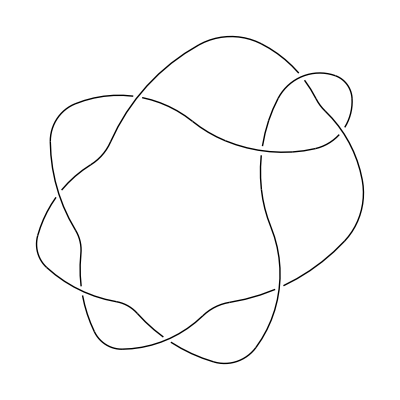

```mathematica
Show[DrawPD[mappd[lattice82knotpd]]]
```

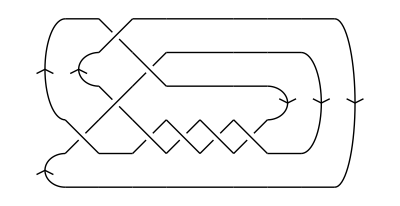

```mathematica
drawpd[lattice82knotpd]
```

```mathematica
Show[Graphics3D[prettyReturn[polygonFromPD[lattice82knotpd],0.1]]]
```

-Graphics3D-

```mathematica
trefcomposite={{0.522206,0.316536,0.009893},{0.926117,-0.798583,0.028876},{1.693196,-1.704427,0.083108},{2.732734,-2.278795,0.189816},{3.908075,-2.440639,0.367796},{5.065424,-2.188501,0.635896},{6.112322,-1.628738,1.008334},{7.093021,-0.95125,1.44281},{8.095791,-0.279627,1.759965},{9.110248,0.391885,1.753832},{10.018056,1.062116,1.345489},{10.681102,1.68931,0.578511},{11.003092,2.221021,-0.433214},{10.944182,2.614531,-1.549486},{10.514748,2.841604,-2.6289},{9.765472,2.891129,-3.54358},{8.778624,2.769313,-4.186978},{7.661397,2.500782,-4.479791},{6.53712,2.128506,-4.377513},{5.535854,1.714007,-3.87876},{4.772917,1.333069,-3.034181},{4.313907,1.06026,-1.944359},{4.124056,0.929653,-0.726737},{4.071296,0.86842,0.533362},{4.087943,0.684687,1.768715},{4.246746,0.220207,2.889414},{4.615878,-0.526694,3.76585},{5.192608,-1.447463,4.281242},{5.920839,-2.394766,4.37606},{6.718348,-3.226413,4.053571},{7.495731,-3.824036,3.36923},{8.167327,-4.102219,2.419993},{8.66083,-4.014031,1.333496},{8.924518,-3.555454,0.258338},{8.937159,-2.769502,-0.650911},{8.718566,-1.746668,-1.254879},{8.336386,-0.608836,-1.470404},{7.888372,0.54094,-1.326308},{7.426258,1.666132,-0.989257},{6.863438,2.725673,-0.650875},{6.067469,3.611144,-0.387681},{5.029669,4.192747,-0.203399},{3.854553,4.380533,-0.085351},{2.68771,4.150405,-0.019378},{1.670775,3.536851,0.009136},{0.920802,2.617932,0.0143},{0.522206,1.501665,0.009893},{-0.431777,1.489862,0.009893},{-0.827084,2.605301,0.004041},{-1.571218,3.526676,0.005326},{-2.581247,4.147504,0.026763},{-3.743521,4.390701,0.081741},{-4.919639,4.219621,0.184572},{-5.964644,3.653153,0.350648},{-6.764459,2.773525,0.594321},{-7.304836,1.706986,0.92019},{-7.708334,0.565284,1.278085},{-8.093809,-0.602533,1.496591},{-8.437513,-1.771226,1.382791},{-8.646162,-2.847658,0.87287},{-8.647603,-3.70352,0.028145},{-8.415944,-4.23591,-1.020468},{-7.966841,-4.390701,-2.118649},{-7.34561,-4.163319,-3.114727},{-6.618512,-3.594717,-3.87466},{-5.863704,-2.766052,-4.293441},{-5.164119,-1.793298,-4.304399},{-4.59649,-0.817958,-3.890732},{-4.216683,0.008328,-3.095905},{-4.036457,0.561796,-2.024288},{-4.004036,0.813499,-0.808121},{-4.044804,0.889643,0.451144},{-4.200627,0.988515,1.683962},{-4.611051,1.207145,2.811193},{-5.334982,1.527177,3.718251},{-6.320396,1.881876,4.295524},{-7.45314,2.200892,4.479791},{-8.599049,2.426126,4.261662},{-9.627818,2.517221,3.678366},{-10.425595,2.451708,2.804175},{-10.902935,2.224358,1.74352},{-11.003092,1.846591,0.623584},{-10.709976,1.345071,-0.412981},{-10.058413,0.76044,-1.222669},{-9.140487,0.140684,-1.683768},{-8.095375,-0.47531,-1.740347},{-7.050701,-1.087366,-1.453847},{-6.033001,-1.709393,-1.021529},{-4.967355,-2.233568,-0.638316},{-3.806181,-2.467194,-0.360499},{-2.632831,-2.295596,-0.176451},{-1.596671,-1.716411,-0.066116},{-0.833275,-0.808624,-0.010149},{-0.431777,0.306176,0.009893},{0.522206,0.316536,0.009893}};
```

```mathematica
plotlist[trefcomposite]
```

-Graphics3D-95

```mathematica
trefcompositepd=nicerPD[trefcomposite,1]
```

{{1,5,2,4},{5,3,6,2},{3,7,4,6},{7,11,8,10},{11,9,12,8},{9,1,10,12}}

```mathematica
decomposePD[trefcompositepd]
```

{{{6,4,1,3},{4,2,5,1},{2,6,3,5}},{{1,5,2,4},{3,1,4,6},{5,3,6,2}}}

```mathematica
lookuppd[{{6,4,1,3},{4,2,5,1},{2,6,3,5}}]
```

{3_1,{{2}},{{6,4,1,3},{4,2,5,1},{2,6,3,5}},-1/v^4+2/v^2+z^2/v^2}

```mathematica
lookuppd[{{1,5,2,4},{3,1,4,6},{5,3,6,2}}]
```

{3_1,{{2}},{{1,5,2,4},{3,1,4,6},{5,3,6,2}},-1/v^4+2/v^2+z^2/v^2}

```mathematica
lookuppd[trefcompositepd]
```

{3_1!#3_1!,{{10}},{{1,5,2,4},{5,3,6,2},{3,7,4,6},{7,11,8,10},{11,9,12,8},{9,1,10,12}},1/v^8-4/v^6+4/v^4-(2 z^2)/v^6+(4 z^2)/v^4+z^4/v^4}

```mathematica
IdentifyWithin[mappd[trefcompositepd],AllKnots[]]
```

KnotTheory::loading: Loading precomputed data in Jones4Knots`.

KnotTheory::loading: Loading precomputed data in Jones4Knots11`.

KnotTheory::credits: The Kauffman polynomial program was written by Scott Morrison.

{ConnectedSum[Mirror[Knot[3,1]],Mirror[Knot[3,1]]]}

### Display Tools

1. plotlist[lst] generated a 3D plot of the polygon with red vertices, start/edn vertex in blue and an arrow for the direction. Also lists the length+1 of the polygon.

2. project[lst_] projects into the x-y plane by deleting the z-coordinate.

3. prettyReturn[lst_, rad_] makes a list of cylinders of radius rad to created a pretty plot.
Limitations: If rad is big cylinders intersect, need to run Graphics3D on the output to creat the plot.

3. prettyReturn[lst_,n,  rad_] makes a list of cylinders of radius rad to created a pretty plot. n is the vertix that is highlighted in red by making the two adjacent cylinders red.
Limitations: If rad is big cylinders intersect, need to run Graphics3D on the output to creat the plot.

4. PolyinSphere[v_,rad_,confinmentR,offset] plots the polygon using the pretty return cylinders to gether with a sphere of radius confinmentR and center {0,0,offset}.

```mathematica
plotlist[testpoly]
```

-Graphics3D-21

```mathematica
project[testpoly]
```

{{0,0},{0.202732,-0.290572},{-0.56167,0.334592},{0.222324,0.942812},{-0.55338,1.00416},{-0.188948,0.140647},{0.463592,0.5627},{0.728278,0.319897},{0.339108,0.424317},{-0.0963369,1.31903},{0.614072,0.894077},{-0.104327,0.258841},{-0.617606,-0.511012},{-0.760091,-0.16827},{-1.3333,0.463809},{-0.706333,0.321441},{-0.127237,0.0681882},{-0.0459604,-0.879099},{-0.736555,-1.05212},{-0.944464,-0.0827903},{0,0}}

```mathematica
Graphics3D[prettyReturn[testpoly,.1]]
```

-Graphics3D-

```mathematica
Graphics3D[prettyReturn[testpoly,5,.1]]
```

-Graphics3D-

```mathematica
v=generateConfinedPolygon[20,0,1,10^-10]
```

{{0,0,0},{-0.574548,-0.685911,-0.446564},{0.304252,-0.390176,-0.0720638},{0.317881,0.384754,0.559836},{-0.319545,-0.36725,0.391974},{0.169277,-0.467707,-0.474607},{-0.448372,-0.36907,0.305637},{-0.305825,0.0368123,-0.597103},{0.537671,-0.331032,-0.205687},{0.279105,0.606205,0.0282596},{-0.51708,0.128515,0.399611},{0.068517,0.61508,-0.248717},{-0.590643,0.09453,0.293994},{-0.231284,-0.248019,-0.574062},{0.00590115,-0.572391,0.341649},{0.660691,0.0762867,-0.0462526},{-0.169423,0.606534,-0.218732},{-0.307396,-0.349571,-0.477241},{0.301658,-0.514058,0.298644},{-0.664604,-0.499404,0.555785},{0,0,0}}

```mathematica
PolyinSphere[v,.05,1,0]
```

-Graphics3D-

```mathematica
v=generateConfinedPolygon[30,0.7,1,10^-10]
PolyinSphere[v,.02,1,0.7]
```

{{0,0,0},{0.155816,-0.483502,0.861363},{-0.729131,-0.523172,0.397364},{-0.475403,0.309279,0.889958},{0.254741,0.903847,0.553239},{0.354902,-0.0236436,0.913418},{-0.102272,0.718591,0.42344},{-0.406129,-0.101147,-0.0620488},{-0.739662,0.349769,0.765859},{-0.0397164,-0.0730886,1.34142},{-0.119043,-0.784933,0.643574},{-0.620305,0.078818,0.591885},{-0.27496,-0.818349,0.316517},{0.394278,-0.226246,0.765443},{-0.578649,-0.373222,0.587086},{0.176533,0.227168,0.850205},{-0.743233,0.224202,0.457749},{-0.182196,-0.577151,0.665285},{-0.706945,0.256854,0.494776},{0.229638,0.565044,0.661602},{0.549869,-0.380452,0.602526},{-0.132815,0.312859,0.833313},{-0.0017309,-0.654744,0.617529},{0.807682,-0.118103,0.379058},{0.074387,-0.797268,0.410899},{-0.7719,-0.265494,0.379051},{0.084765,-0.776973,0.44624},{0.683574,0.0117523,0.58531},{0.0746358,0.788936,0.426627},{-0.824998,0.35255,0.441686},{0,0,0}}

-Graphics3D-

```mathematica
v=generateConfinedPolygon[50,0.7,1,10^-10]
PolyinSphere[v,.02,1,0.7]
```

{{0,0,0},{0.745613,-0.0249918,0.665911},{0.0355487,-0.0980535,1.36625},{0.0463531,0.814904,0.958335},{0.43949,0.0340904,0.47277},{-0.448972,-0.178532,0.879497},{0.546244,-0.245588,0.950543},{-0.0953923,0.44681,1.28053},{0.774469,0.180758,0.865125},{-0.137215,-0.10316,0.568104},{0.76739,-0.455644,0.807777},{0.216977,-0.183392,0.0185221},{0.0718012,-0.291275,1.00203},{-0.262203,-0.416904,0.0678669},{0.0192793,0.238469,0.768762},{-0.204795,-0.180361,1.64875},{-0.880677,-0.271186,0.917355},{-0.209835,-0.507332,0.214357},{-0.130644,0.485595,0.302807},{-0.67759,-0.343362,0.185844},{0.249011,0.00150326,0.0359156},{-0.358848,0.393795,0.726288},{0.467401,0.448521,0.165648},{-0.16293,-0.25912,-0.153613},{0.0153846,-0.803239,0.666228},{0.711181,-0.0961047,0.540414},{0.283446,-0.122425,1.44394},{0.224615,-0.189237,0.447906},{-0.145037,0.260122,1.26119},{0.468909,-0.488613,1.01126},{-0.356424,-0.734137,0.502787},{-0.654731,0.219939,0.530216},{-0.148267,-0.635148,0.641217},{-0.746288,0.147211,0.467189},{0.145672,-0.00805956,0.891803},{-0.705847,0.299932,0.467473},{-0.246917,-0.568842,0.653528},{-0.669177,0.325454,0.50543},{0.103184,-0.192307,0.873374},{-0.349736,0.632833,0.535725},{0.278162,-0.0781138,0.852424},{-0.684288,-0.0557944,0.581881},{0.278096,-0.0670287,0.853344},{-0.341572,-0.720113,0.418035},{-0.051679,0.111593,0.891562},{-0.640754,0.585787,0.237245},{0.334007,0.729157,0.408376},{0.688271,-0.195831,0.545832},{0.304249,0.721777,0.443251},{0.276387,-0.139342,0.950891},{0,0,0}}

-Graphics3D-

### Knot Finder

1. lookupdt[dt_]
Given a DT code of a knot this will look up what knot it is using the HOMFLYPT as identifier.
Limitations: Works for knots up to including 9 crossings, connected sums up to eight crossings. Mirror images are grouped together.
Conversion of DT code into PD code does not work correctly if the knot is a connected sum, we need to split the DT code into diagrammatically prime factors before calling this function.

Return : {knot in Rolfson notation, {{positions of knot in our list}}, DT code, HOMFLYPT polynomial}

2. lookuppd[pd_]
Given a PD code of a knot this will look up what knot it is using the HOMFLYPT as identifier.
Limitations: Works for knots up to including 9 crossings, connected sums up to eight crossings. Mirror images are grouped together.

Return : {knot in Rolfson notation, {{positions of knot in our list}}, PD code, HOMFLYPT polynomial}

3. getstr[x_]
Tell you the knot located in position x in our list.
Limiations: List contains knots up to including 9 crossings, connected sums up to eight crossings. Mirror images are grouped together.
The length of the list is 101, elements 100 are not found and 101 unknown. Not found means a HOMFLYPT calculations resulted into a polynomial not in the list, unknown means calculations broke down somewhere.

```mathematica
lookupdt[{-14,-10,-12,-16,-2,-4,-6,-8}]
```

KnotTheory::credits: "The GaussCode to PD conversion was written by Siddarth Sankaran at the University of Toronto in the summer of 2005."

{8_2,{{22}},{-14,-10,-12,-16,-2,-4,-6,-8},3 v^2-3 v^4+v^6+4 v^2 z^2-7 v^4 z^2+3 v^6 z^2+v^2 z^4-5 v^4 z^4+v^6 z^4-v^4 z^6}

```mathematica
lookupdt[{14,10,12,16,2,4,6,8}]
```

{8_2,{{22}},{14,10,12,16,2,4,6,8},1/v^6-3/v^4+3/v^2+(3 z^2)/v^6-(7 z^2)/v^4+(4 z^2)/v^2+z^4/v^6-(5 z^4)/v^4+z^4/v^2-z^6/v^4}

```mathematica
lookupdt[{-24,18,8,14,16,-10,-6,-12,-22,-26,4,28,-20,-2}]
```

{Not Found,{-24,18,8,14,16,-10,-6,-12,-22,-26,4,28,-20,-2},√v+v-v^(5/2)+v^4+2 v^(9/2)+2 v^5+v^(11/2)+v^6-2 v^(13/2)-3 v^7-v^(15/2)-3 v^8+v^(17/2)+2 v^9+v^(19/2)+3 v^10-v^(21/2)-v^11-v^12+v^4 z^2+v^5 z^2+v^(11/2) z^2-v^7 z^2-v^(15/2) z^2-v^8 z^2+v^(19/2) z^2+v^10 z^2}

```mathematica
lookupdt[{10,-8,14,-16,18,-6,4,12,2}]
```

{7_1,{{12}},{10,-8,14,-16,18,-6,4,12,2},-3/v^8+4/v^6-(4 z^2)/v^8+(10 z^2)/v^6-z^4/v^8+(6 z^4)/v^6+z^6/v^6}

The example below showes how this fails for a diagrammatically non-prime diagram. The DT code actually presents the unknot.

```mathematica
completedt[{-24,18,8,14,16,-10,-6,-12,-22,-26,4,28,-20,-2}]
```

{{1,-24},{-2,27},{3,18},{4,21},{5,8},{-6,13},{7,14},{8,5},{9,16},{-10,11},{11,-10},{-12,15},{13,-6},{14,7},{15,-12},{16,9},{17,-22},{18,3},{19,-26},{-20,25},{21,4},{-22,17},{23,28},{-24,1},{25,-20},{-26,19},{27,-2},{28,23}}

```mathematica
decomposedt[{{1,-24},{-2,27},{3,18},{4,21},{5,8},{-6,13},{7,14},{8,5},{9,16},{-10,11},{11,-10},{-12,15},{13,-6},{14,7},{15,-12},{16,9},{17,-22},{18,3},{19,-26},{-20,25},{21,4},{-22,17},{23,28},{-24,1},{25,-20},{-26,19},{27,-2},{28,23}}]
```

{{{1,-12},{-2,15},{3,6},{4,9},{5,-10},{6,3},{7,-14},{-8,13},{9,4},{-10,5},{11,16},{-12,1},{13,-8},{-14,7},{15,-2},{16,11}},{{1,4},{-2,7},{3,8},{4,1},{5,10},{-6,9},{7,-2},{8,3},{9,-6},{10,5}},{{-1,2},{2,-1}}}

PD examples

```mathematica
lookuppd[{{1,24,2,25},{27,2,28,3},{18,4,19,3},{4,22,5,21},{8,5,9,6},{13,7,14,6},{14,7,15,8},{16,9,17,10},{11,11,12,10},{15,13,16,12},{17,22,18,23},{19,26,20,27},{25,20,26,21},{28,24,1,23}}]
```

{0_1,{{1}},{{1,24,2,25},{27,2,28,3},{18,4,19,3},{4,22,5,21},{8,5,9,6},{13,7,14,6},{14,7,15,8},{16,9,17,10},{11,11,12,10},{15,13,16,12},{17,22,18,23},{19,26,20,27},{25,20,26,21},{28,24,1,23}},1}

```mathematica
lookuppd[{{10,2,11,1},{2,18,3,17},{3,9,4,8},{4,14,5,13},{14,6,15,5},{11,7,12,6},{7,17,8,16},{18,10,1,9},{12,16,13,15}}]
```

{7_1,{{12}},{{10,2,11,1},{2,18,3,17},{3,9,4,8},{4,14,5,13},{14,6,15,5},{11,7,12,6},{7,17,8,16},{18,10,1,9},{12,16,13,15}},-3/v^8+4/v^6-(4 z^2)/v^8+(10 z^2)/v^6-z^4/v^8+(6 z^4)/v^6+z^6/v^6}

```mathematica
lookuppd[{{1,9,2,8},{15,2,16,3},{11,4,12,5},{5,12,6,13},{13,6,14,7},{7,14,8,15},{9,1,10,16},{3,10,4,11}}]
```

{8_2,{{22}},{{1,9,2,8},{15,2,16,3},{11,4,12,5},{5,12,6,13},{13,6,14,7},{7,14,8,15},{9,1,10,16},{3,10,4,11}},3 v^2-3 v^4+v^6+4 v^2 z^2-7 v^4 z^2+3 v^6 z^2+v^2 z^4-5 v^4 z^4+v^6 z^4-v^4 z^6}

```mathematica
getstr[12]
getstr[99]
getstr[100]
getstr[101]
```

7_1

9_49

Not Found

Unknown

## Random Polygon Generation

#### global parameters

```mathematica
RANDOMWORKINGPRECISION=90;
```

```mathematica
volumeFuncs = {} ;  (* contain the volume functions once loaded with initPolyGeneration *)
```

```mathematica
ufuncinv[R_]:=R*x^(1/3);
ufunc[R_]:=x^3/R^3;
```

#### polygon calc functions

```mathematica
(*initPolyGeneration[steps_, R_] := Module[{fileName},
(* find the file with the correct R values and step values *)
fileName = "precomputed volume functions\\volumes2to20R" <> ToString[R 10] <> "new.wdx";
volumeFuncs= Import[fileName];
volumeFuncs =If [steps> 20
,  Join[volumeFuncs,Table[{i,R,Import["precomputed volume functions\\volumes" <> ToString[i] <> "50R" <> ToString[10 R] <> "new.wdx"]}, {i, 21, steps}]]
, volumeFuncs];
]*)
```

```mathematica
(* June 8, 2012  
for additional steps each step is in a differnt file..
for R =1.1, 1.2, .... the names of the files are different: 50 is dropped *)initPolyGeneration[steps_,R_]:=Module[{fileName},(*find the file with the correct R values and step values*)
If[R≤4 && FractionalPart[R*2] == 0
,fileName="volumefunctions/volumes2to20R"<>ToString[R 10]<>"new.wdx";
volumeFuncs=Import[fileName];
volumeFuncs=If[steps>20
,  Join[volumeFuncs,Table[{i,R,Import["volumefunctions/volumes"<>ToString[i]<>"50R"<>ToString[10 R]<>"new.wdx"]},{i,21,steps}]]
,volumeFuncs
];
, (* R ≥ 4 || not a halfstep *)

If[FractionalPart[2 * R] == 0 
,(* halfstep 4.5 or lager ... actually only 4.5 so far.... 
first 80 contain 50R, after that no longer... *)
volumeFuncs=
Join[{{1,10 R,Null}},
 Table[{i,R,Import["volumefunctions/volumes"<>ToString[i]<>"50R"<>ToString[10 R]<>"new.wdx"]},{i,2,80}],Table[{i,R,Import["volumefunctions/volumes"<>ToString[i]<>"R"<>ToString[10 R]<>"new.wdx"]},{i,81,90}]];
, (* not a halfstep *)volumeFuncs=Join[{{1,10 R,Null}},Table[{i,R,Import["volumefunctions/volumes"<>ToString[i]<>"R"<>ToString[10 R]<>"new.wdx"]},{i,2,steps}]]]]]
```

```mathematica
(* compute part of the volumnefunction which does not depend on r *)volumePartI[Rnum_, Rdenom_,kStart_, kEnd_]:=Module[{func, ind},
If[kStart==1,func=1,func=Import["volumesPartI" <> ToString[kStart-1] <> "R" <> ToString[Rnum/Rdenom 10] <> ".wdx"]];
(* output part func for k=1 *)
If[kStart==1,Export["volumesPartI1R" <> ToString[Rnum/Rdenom 10] <> ".wdx", func]];
(* compute next volumePartI functions and store them all *)
For[ind=Max[2,kStart],ind≤kEnd,ind++,
func=Integrate[func/.t->x,{x,Abs[t-1],Max[Min[Rnum/Rdenom,ind,t+1],Abs[t-1]]},Assumptions->{Im[t]==0&&Im[Rnum/Rdenom]==0}];
Export["volumesPartI" <> ToString[ind] <> "R" <> ToString[Rnum/Rdenom 10] <> ".wdx", func]];

];
```

```mathematica
(* comopute the final volume function - reading the first part from a file *)volumePartII[k_,tkp1_,R_,r_]:=Module[{func, ind},
func=Import["volumesPartI" <> ToString[k-1] <> "R" <> ToString[R 10] <> ".wdx"];
If[k≥2,
func=Integrate[func/.t->x,{x,Abs[tkp1-1],Max[Min[R,k,r,tkp1+1],Abs[tkp1-1]]},Assumptions->{Im[tkp1]==0&&Im[R]==0&&Im[r]==0}];
];
Return[func];
]
```

```mathematica
genVolumePartII[Rnum_, Rdenom_, kStart_, kEnd_] := Module [{i},
	For[i=kStart, i≤kEnd,i++,
		Export["volumes" <> ToString[i] <> "R" <> ToString[Rnum/Rdenom 10] <> "new.wdx", volumePartII[i,tkp1,Rnum/Rdenom,r]]]]
```

```mathematica
volume[k_,tkp1_,R_,r_]:=Module[{func, ind},
func=1;
For[ind=2,ind≤k-1,ind++,
func=Integrate[func/.t->x,{x,Abs[t-1],Max[Min[R,ind,t+1],Abs[t-1]]},Assumptions->{Im[t]==0&&Im[R]==0}];
];
If[k≥2,
func=Integrate[func/.t->x,{x,Abs[tkp1-1],Max[Min[R,k,r,tkp1+1],Abs[tkp1-1]]},Assumptions->{Im[tkp1]==0&&Im[R]==0&&Im[r]==0}];
];
Return[func];
]
```

```mathematica
(* 'short' functions remove the first factor of I_n(t), since it is cancelled anyway *)
sumfuncshort[n_,t_]:=
Sum[(-1)^i*(t+n-2*i)^(n-1)/(i!*(n-i)!),{i,0,Ceiling[(t+n)/2]-1,1}]
```

```mathematica
(* just calculate the denominator *)cdfvalCalcDeno[n_,t_]:=sumfuncshort[n,t+1]-sumfuncshort[n,Abs[t-1]]
```

```mathematica
(* calculate the cdf WITHOUT dividing by the denominator AND without subtracting the second part*)
cdfvalNoDenoNoSub[n_,x_]:=  sumfuncshort[n,x]
```

```mathematica
(* calculate subtraction part *)
cdfvalSub[n_,t_]:=  sumfuncshort[n,Abs[t-1]]
```

```mathematica
cdfvalshort[n_,t_,x_]:=Module[{},
(sumfuncshort[n,x]-sumfuncshort[n,Abs[t-1]])/(sumfuncshort[n,t+1]-sumfuncshort[n,Abs[t-1]])
]
```

```mathematica
cdfvalshortNoDenom[n_,t_,x_]:=Module[{},
(sumfuncshort[n,x]-sumfuncshort[n,Abs[t-1]])
]
```

```mathematica
cdfvalforceConfineClose[steps_, tau_,  R_, p_] :=
	(*cdfvalshortNoDenom[steps, tau, p]/cdfvalshortNoDenom[steps, tau, R]*)Evaluate[Apply[Function, List[{tkp1,r}, volumeFuncs[[steps,3]]]]][tau,p]/Evaluate[Apply[Function, List[{tkp1,r}, volumeFuncs[[steps,3]]]]][tau,R]
```

```mathematica
cdfvalforceConfine[steps_, tau_,  R_, p_] :=
	cdfvalshort[steps, tau, p]Evaluate[Apply[Function, List[{tkp1,r}, volumeFuncs[[steps,3]]]]][tau,p]/Evaluate[Apply[Function, List[{tkp1,r}, volumeFuncs[[steps,3]]]]][tau,R]
```

```mathematica
circparmat[p_,r_]:=
Module[{h,t,θ,ρ,rad},
(*distance of point from origin*)
t=Sqrt[p.p];
(*radius of circle intersection*)
h=Sqrt[(1/2)*((1+r^2)-((t^4+(r^2-1)^2)/(2*t^2)))];
ρ=ArcCos[p[[3]]/t];
θ=If[p[[1]]==0,If[p[[2]]≥ 0,Pi/2,-Pi/2],If[p[[1]]≥ 0,ArcTan[p[[2]]/p[[1]]],Pi+ArcTan[p[[2]]/p[[1]]]]];
rad=If[(r^2+t^2)≥1,Sqrt[r^2-h^2],-Sqrt[r^2-h^2]];
(*Print["t ",N[t]];
Print["h ",N[h]];
Print["ρ ",N[ρ]];
Print["θ ",N[θ]];
Print["rad ",N[rad]];*)
RotationMatrix[θ,{0,0,1}].RotationMatrix[ρ,{0,1,0}].{h*Cos[u],h*Sin[u],rad}]
```

```mathematica
circMat[p_,r_]:=
Module[{h,t,θ,ρ,rad, u},
(*distance of point from origin*)
t=Sqrt[p.p];
(*radius of circle intersection*)
h=Sqrt[(1/2)*((1+r^2)-((t^4+(r^2-1)^2)/(2*t^2)))];
ρ=ArcCos[p[[3]]/t];
θ=If[p[[1]]==0,If[p[[2]]≥ 0,Pi/2,-Pi/2],If[p[[1]]≥ 0,ArcTan[p[[2]]/p[[1]]],Pi+ArcTan[p[[2]]/p[[1]]]]];
rad=If[(r^2+t^2)≥1,Sqrt[r^2-h^2],-Sqrt[r^2-h^2]];
(*Print["t ",N[t]];
Print["h ",N[h]];
Print["ρ ",N[ρ]];
Print["θ ",N[θ]];
Print["rad ",N[rad]];*)
u= RandomReal[{0, 2Pi},WorkingPrecision->RANDOMWORKINGPRECISION];
RotationMatrix[θ,{0,0,1}].RotationMatrix[ρ,{0,1,0}].{h*Cos[u],h*Sin[u],rad}]
pickSphericalCoordinates[]:= Module [{ u, v } , (* Based on Wolfram publication*)
(*u=IntegerPart[RandomReal[] 10^16]/10^16;
v=IntegerPart[RandomReal[] 10^16]/10^16;*)
u=RandomReal[{0,1},WorkingPrecision->RANDOMWORKINGPRECISION];
v=RandomReal[{0,1},WorkingPrecision->RANDOMWORKINGPRECISION];
 Return[{ 2 Pi u, ArcCos[2 v -1]}]]
convertSphericalsToPoint[{theta_, phi_}] := Module [{ x, y, z} ,  (* based on Wolfram Pub on spherical coordinates *)
x = Cos[theta] Sin[phi];
y =Sin[theta]Sin[phi];
z = Cos[phi];
Return[{x,y,z}]]
```

```mathematica
gettrans[{theta_,phi_}]:=RotationMatrix[theta,{0,0,1}].RotationMatrix[phi,{0,1,0}]
```

```mathematica
pexact[k_, tau_, r_] :=((k-1)/(k+1))(Sum[UnitStep[2j-k-r](-1)^j  (r+k-2j)^(k-2)/(Factorial[k-j]Factorial[j]) ,{j,0,k}])/(Sum[UnitStep[2j-k-1-tau](-1)^j (tau+k+1-2j)^(k-1)/(Factorial[k+1-j]Factorial[j]) ,{j,0,k+1}]);
```

```mathematica
pickR[v_, tau_] := √((tau-1)^2+4 v tau);
```

```mathematica
q[tau_, r_] := Piecewise[{{r/(2 tau), Abs[tau-1] ≤ r ≤ tau+1}},0] ;
```

```mathematica
vforR[R_, tau_] := (-1+R^2+2 tau-tau^2)/(4 tau);
```

```mathematica
findrad[n_,t_,u_,acc_,R_]:=Module[{left,right,done=False,pos,ct=0,val=0, useFunc, denom1, denom2},
left=Abs[t-1];
right=Min[n,t+1,R];
(* Print ["left  right ", left //N, " ", right //N ]; *)
(* check special values *)
If[u==1,
	Return[{ct, right}]];
If[u==0,
	Return[{ct, left}]];
done=False;
(* useFunc = volumeFuncs[[n,3]] /. tkp1-> t;*)
(* Print["useFunc " , useFunc]; *)
(* Print["useFunc = ",useFunc]; *)
denom2 = Evaluate[Apply[Function, List[{tkp1,r}, volumeFuncs[[n,3]]]]][t,R];
While[!done  && ct < 150,
ct++;
pos=(left+right)/2;
(* If[n==3,Print["pos = ",pos , " and ", left, " ", right, " ", Abs[u-val]//N];]; *)
(* val=cdfvalshortNoDenom[n, t, pos]/denom1 (Evaluate[Apply[Function, List[{r}, useFunc]]][pos])/denom2;  *)
 val=1/denom2 Evaluate[Apply[Function, List[{tkp1,r}, volumeFuncs[[n,3]]]]][t,pos];  
(* val=cdfvalshortNoDenom[n, t, pos]/denom1 useFunc[pos]/denom2; *)
(*Print ["left pos right val ", left //N, " ", pos //N, " ", right //N , " ", val //N]; *)
If[ct== 150, Print["count limited findrad with t+1 > R for steps = ", n,  "and tau = ", t ," and u = ", u]];
If[Abs[u-val]<acc,
	Return[{ct,pos }]];

If [u < val, 
	right=pos; ,
	left = pos;];
	
];

]
```

```mathematica
findradfaster[n_,t_,u_,acc_,R_]:=Module[{left,right,denominator,done=False,pos,ct=0,val,valold, newu, newacc, sub},
left=Abs[t-1];
right=Min[n,t+1,R];
(* check special values *)
If[u==1,
	Return[{ct, right}]];
If[u==0,
	Return[{ct, left}]];
(* compute the common denominator *)
denominator=cdfvalCalcDeno[n, t];
sub = cdfvalSub[n,t];
newu=u * denominator + sub;
(* Print[ "demo = ", N[denominator], " and sub = ", N[sub]]; *)
If [denominator > 0,
newacc= acc*denominator;
done=False;
While[!done  ,
ct++;
pos=(left+right)/2;
val=cdfvalNoDenoNoSub[n, pos];

If[Abs[newu-val]<newacc,
	Return[{ct, pos }]];

If [newu > val, 
	left=pos; ,
	right = pos;];

];,
(* do the same with the inequality sign changed *)
newacc=- acc*denominator;
done=False;

While[!done ,
ct++;
pos=(left+right)/2;
val=cdfvalNoDenoNoSub[n,pos];

If[Abs[newu-val]<newacc,
	Return[{ct,pos }]];

If [newu < val, 
	left=pos; ,
	right = pos;];
	
];
];
]
```

```mathematica
determineR[tau_,R_,remainingSteps_,acc_]:=Module[
{newR,u,v,done=False,r,pr,qr,ct=0,t,umod=1,vmod=1,uuse,c,noaccrej=False},
t=SetPrecision[tau,Infinity];
(* If[t+1>R&&remainingSteps≥ R,
umod=cdfvalshort[remainingSteps,t,R];
]; *)
u=SetPrecision[umod RandomReal[{0,1},WorkingPrecision->RANDOMWORKINGPRECISION],Infinity];
newR=findrad[remainingSteps,t,u,acc,R];
Return[{0,newR[[2]]}];
]
```

```mathematica
generateConfinedPolygon[steps_,centerZValue_,confinementRadius_,acc_]:=Module[{origin={0,0,0},ptlst,center={0,0,centerZValue},print=False,remainingSteps,pt,temppt,dist,newR,methretryct,methct,retryct,totmethretry=0,totmeth=0,totretries=0,done=False,validPolygon=False,polygonRetry=0},
(* generate a polygon until it's valid *)
While[!validPolygon,
remainingSteps=steps-2;
ptlst={};
totretries=0;
totmethretry=0;
totmeth=0;

If[print,
Print[origin];
];
(* pick the first point and make sure it's in confinement - repeat if needed *)
AppendTo[ptlst,origin];
retryct=0;
pt=convertSphericalsToPoint[pickSphericalCoordinates[]];
done=EuclideanDistance[pt,center]≤confinementRadius;
While[!done,
pt=convertSphericalsToPoint[pickSphericalCoordinates[]];
done=EuclideanDistance[pt,center]≤confinementRadius;
retryct++;
];

(* dist becomes the tau value for the next iteration *)
dist=1;
(* the point is added to the polygon *)
AppendTo[ptlst,N[pt]];

totretries+=retryct;
If[print,
Print["   dist from last pt ",N[EuclideanDistance[pt,ptlst[[-2]]]]];
Print["rem steps ",steps-1," pt ",N[pt]," retryct ",retryct," methct ",0];
];

While[remainingSteps>1,
(* check whether we are at the origin*)
If[dist==0,
retryct=0;
pt = convertSphericalsToPoint[pickSphericalCoordinates[]]; 
done=EuclideanDistance[pt,center]≤confinementRadius;
While[!done,
pt=convertSphericalsToPoint[pickSphericalCoordinates[]];
done=EuclideanDistance[pt,center]≤confinementRadius;
retryct++;
];
dist=1;
AppendTo[ptlst, N[pt]];
remainingSteps--;
totretries+=retryct;
If[print,
Print["   dist from last pt ",N[EuclideanDistance[pt,ptlst[[-2]]]]];
Print["rem steps ",remainingSteps," pt ",N[pt]," retryct ",retryct," methct ",0];
];
Continue[];
];
(* check if we are remainingSteps +1 away and must walk straight towards the origin *)
If[dist==remainingSteps+1,
pt=(dist-1)/dist*pt;
dist=remainingSteps;
AppendTo[ptlst,N[pt]];
remainingSteps--;
If[print,
Print["   dist from last pt ",N[EuclideanDistance[pt,ptlst[[-2]]]]];
Print["rem steps ",remainingSteps," pt ",N[pt]," retryct ",retryct," methct ",0];
];
Continue[];
];

(* none of the special cases - so generate the next point using the cdf   - repeat if not in confinement*)
methct=0;
retryct=0;
newR=determineR[dist,confinementRadius+Abs[centerZValue],remainingSteps,acc];
If[newR==Null,
polygonRetry++;
Print["Null from newR...restarting"];
Break[];
];
methct+=newR[[1]];
temppt=circMat[pt,newR[[2]]];
done=EuclideanDistance[temppt,center]≤confinementRadius;
While[!done,
newR=determineR[dist,confinementRadius+Abs[centerZValue],remainingSteps,acc];
If[newR==Null,
polygonRetry++;
Print["Null from newR...restarting"];
Break[];
];
methct+=newR[[1]];
temppt=circMat[pt,newR[[2]]];
done=EuclideanDistance[temppt,center]≤confinementRadius;
retryct++;
If[retryct>100,
polygonRetry++;
Print["Unexpectedly large number of retries...restarting!"];
Break[];
];
];
totretries+=retryct;
totmeth+=methct;
pt=temppt;
AppendTo[ptlst,N[pt]];
dist=newR[[2]];
If[print,
Print["   dist from last pt ",N[EuclideanDistance[pt,ptlst[[-2]]]]," newR ",N[newR[[2]]]];
Print["rem steps ",remainingSteps," pt ",pt," retryct ",retryct," methct ",methct];
];
remainingSteps--;

];(*close while remainingsteps*)

(* generate X1 on the intersection circle of a unit sphere around the origin and around the current point *)
If[Length[ptlst]==(steps-1),
temppt=circMat[pt,1];
done=EuclideanDistance[temppt,center]≤confinementRadius;
retryct=0;
While[!done,
temppt=circMat[pt,1];
done=EuclideanDistance[temppt,center]≤confinementRadius;
retryct++;
If[retryct>40,
polygonRetry++;
If[print,
Print["Impossible to close polygon...restarting!"];
];
Break[];
];
];
If[!done,Continue[]];
totretries+=retryct;
pt=temppt;
AppendTo[ptlst,N[pt]];
dist=1;
If[print,
Print["   dist from last pt ",N[EuclideanDistance[pt,ptlst[[-2]]]]];
Print["rem steps ",remainingSteps," pt ",N[pt]," retryct ",retryct," methct ",0];
];

AppendTo[ptlst,origin];
If[print,
Print[origin];
];
];(*close ptlst=steps-1 if*)
If[Length[ptlst]==(steps+1),
validPolygon=True;
];
];(*close while validpolygon*)
If[print,
Print["total retries ",totretries,", total method retries ",totmeth,", poly retries ",polygonRetry];
];
Return[ptlst];

](*close module*)
```

```mathematica
(* determineR[tau_,R_,remainingSteps_,acc_]:=Module[
{newR,u,v,done=False,r,pr,qr,ct=0,t,umod=1,vmod=1,uuse,c,noaccrej=False},
t=SetPrecision[tau,Infinity];
If[(remainingSteps≤20||t>5)||noaccrej,
If[t+1>R&&remainingSteps≥ R,
umod=cdfvalshort[remainingSteps,t,R];
];
u=SetPrecision[umod RandomReal[{0,1},WorkingPrecision->RANDOMWORKINGPRECISION],Infinity];
newR=findrad[remainingSteps,t,u,acc,R];
Return[{0,N[newR[[2]]]}];
,
While[!done,
If[t+1>R,
vmod=vforR[R,t];
];
u=SetPrecision[RandomReal[{0,1},WorkingPrecision->RANDOMWORKINGPRECISION],Infinity];
v=SetPrecision[vmod RandomReal[{0,1},WorkingPrecision->RANDOMWORKINGPRECISION],Infinity];;
r=pickR[v,t];
pr=pexact[remainingSteps,t,r];
qr=q[t,r];
ct++;
If[remainingSteps>50,c=3/2;,
If[remainingSteps>40,c=1+t/12;,
If[remainingSteps>30,c=1+t/9;,
c=1+t/5;];];];

If[u≤pr/(c qr),done=True;];
];
Return[{ct,N[r]}];
];
] *)
```

#### random polygon batch functions

```mathematica
generatefixedoffsetfilebatch[steps_,R_,c_,acc_,size_,fileCount_]:=Module[{list,ind},
Which[
R+Abs[c]≤1,
initPolyGeneration[steps,1];
,
R+Abs[c]≤3/2,
initPolyGeneration[steps,3/2];
,
R+Abs[c]≤2,
initPolyGeneration[steps,2];
,
R+Abs[c]≤5/2,
initPolyGeneration[steps,5/2];
,
R+Abs[c]≤3,
initPolyGeneration[steps,3];
,
R+Abs[c]≤7/2,
initPolyGeneration[steps,7/2];
,
R+Abs[c]≤4,
initPolyGeneration[steps,4];
,
True,
Print["confinement and centerz out of range"];
Abort[];
];
For[ind=1,ind≤fileCount,ind++,
Print["File recur ",ind];
list=generatefixedoffsetbatch[steps,R,c,acc,size];
Export["step"<>ToString[steps]<>"R"<>ToString[Numerator[R]]<>"_" <> ToString[Denominator[R]]<>"offset"<>ToString[c*10]<>"batch"<>ToString[ind]<>".wdx",list];
];
]
```

```mathematica
generatefixedoffsetfilebatchstartstop[steps_,R_,c_,acc_,size_,startnum_,stopnum_]:=Module[{list,ind},
For[ind=startnum,ind≤stopnum,ind++,
Print["File recur ",ind];
list=generatefixedoffsetbatch[steps,R,c,acc,size];
Export["step"<>ToString[steps]<>"R"<>ToString[Numerator[R]]<>"_" <> ToString[Denominator[R]]<>"offset"<>ToString[c*10]<>"batch"<>ToString[ind]<>".wdx",list];
];
]
```

```mathematica
generatefixedoffsetbatch[steps_,R_,c_,acc_,size_]:=Module[{seed,poly,lst={},print=False,i},
(*{acc,steps,rad,{cenpt},poly}*)
If[print,
Print["{seed,{time,{acc,steps,rad,{cenpt},poly}}}"];
];
For[i=1,i≤size,i++,
If[Mod[i,100]==0,
Print["   bat recur ",i];
];
seed=RandomInteger[{1,100000000}];
SeedRandom[seed];
(*Print[seed];*)
poly=Timing[generateConfinedPolygon[steps,-c,R,acc]];
AppendTo[lst,{seed,{poly[[1]],{acc,steps,R,{c,0,0},poly[[2]]}}}];
];
Return[lst];
]
```

```mathematica
generatebatchuniform[steps_,confinementRadius_,acc_,size_]:=Module[{seed,lst={},print=False,i},
If[print,
Print["{seed,{time,{acc,steps,rad,{cenpt},poly}}}"];
];
For[i=1,i≤size,i++,
If[Mod[i,100]==0,
Print[" bat recur ",i];
];
seed=RandomInteger[{1,100000000}];
(*Print[seed];*)
SeedRandom[seed];
AppendTo[lst,{seed,randomPolygonUniform[steps,confinementRadius,acc]//Timing}];
];
Return[lst];
]
```

```mathematica
generatebatchdistrib[steps_,confinementRadius_,acc_,size_]:=Module[{seed,lst={},print=False,i},
If[print,
Print["{seed,{time,{acc,steps,rad,{cenpt},poly}}}"];
];
For[i=1,i≤size,i++,
If[Mod[i,100]==0,
Print[" bat recur ",i];
];

seed=RandomInteger[{1,100000000}];
Print["  i ",i," seed ",seed];
SeedRandom[seed];
AppendTo[lst,{seed,randomPolygonDistrib[steps,confinementRadius,acc]//Timing}];
];
Return[lst];
]
```

```mathematica
uniformballpointold[R_]:=Module[{c,sph,the,phi,x,y,z},
c=RandomReal[{0,1},WorkingPrecision->RANDOMWORKINGPRECISION]^(1/3)*R;
sph=pickSphericalCoordinates[];
the=sph[[1]];
phi=sph[[2]];
x=c*Sin[phi]*Cos[the];
y=c*Sin[phi]*Sin[the];
z=c*Cos[phi];
Return[{{c,the,phi},{x,y,z}}];
]
```

```mathematica
uniformballpoint[R_]:=Module[{x,y,z,mag},
x=RandomReal[NormalDistribution[0,1],WorkingPrecision->RANDOMWORKINGPRECISION];
y=RandomReal[NormalDistribution[0,1],WorkingPrecision->RANDOMWORKINGPRECISION];
z=RandomReal[NormalDistribution[0,1],WorkingPrecision->RANDOMWORKINGPRECISION];
mag=Sqrt[RandomReal[ExponentialDistribution[1],WorkingPrecision->RANDOMWORKINGPRECISION]+x^2+y^2+z^2];
Return[R/mag*{x,y,z}];
]
```

```mathematica
distribballpt[R_]:=Module[{c,sph,the,phi,x,y,z},
c=getoffset[R];
sph=pickSphericalCoordinates[];
the=sph[[1]];
phi=sph[[2]];
x=c*Sin[phi]*Cos[the];
y=c*Sin[phi]*Sin[the];
z=c*Cos[phi];
Return[{{c,the,phi},{x,y,z}}];
]
```

```mathematica
getoffset[R_]:=Module[{c,u},
u=RandomReal[{0,1},WorkingPrecision->RANDOMWORKINGPRECISION];
c=ufuncinv[R]/.x->u;
Return[c];
]
```

```mathematica
randomPolygonUniform[steps_,confinementRadius_,acc_]:=Module[{c,poly,pt,R},
pt=uniformballpointold[confinementRadius][[1]];
c=SetPrecision[pt[[1]],Infinity];
poly=generateConfinedPolygon[steps,-c,confinementRadius,acc];
Return[{acc,steps,N[confinementRadius],N[pt],poly}];
]
```

```mathematica
randomPolygonDistrib[steps_,confinementRadius_,acc_]:=Module[{c,poly,pt,R,sph,rand},
rand=distribballpt[confinementRadius];
pt=rand[[1]];
c=SetPrecision[pt[[1]],Infinity];
poly=generateConfinedPolygon[steps,-c,confinementRadius,acc];
Return[{acc,steps,N[confinementRadius],N[pt],poly}];
]
```

#### binning and piecewise functions

```mathematica
cliptopolygonsfilename[filename_]:=Module[{lst,len},
lst=Import[filename];
len=Length[lst];
Drop[Flatten[Drop[Flatten[lst,1],{1,2len,2}],1],{1,2len,2}]
]
```

```mathematica
cliptopolygonslist[list_]:=Module[{len},
len=Length[list];
Drop[Flatten[Drop[Flatten[list,1],{1,2len,2}],1],{1,2len,2}]
]
```

```mathematica
getbinseq[R_,d_]:=Module[{pos,list={0}},
For[i=1,i≤d,i++,
pos=list[[-1]];
AppendTo[list,(R^3/d+pos^3)^(1/3)];
];
Return[list];
]
```

```mathematica
getcount[polylist_,exclude_]:=Module[{ct=0},
If[!exclude,
For[i=1,i≤Length[polylist],i++,
For[j=1,j≤Length[polylist[[i,5]]],j++,
ct++;
];
];
Return[ct];
,
For[i=1,i≤Length[polylist],i++,
For[j=2,j≤Length[polylist[[i,5]]]-1,j++,
ct++;
];
];
Return[ct];
];
]
```

```mathematica
calcr[polylist_]:=Module[{lst={},r},
For[i=1,i≤Length[polylist],i++,
r=polylist[[i,4,1]];
For[j=2,j≤Length[polylist[[i,5]]],j++,
AppendTo[lst,EuclideanDistance[{0,0,-r},polylist[[i,5,j]]]];
];
];
Return[lst];
]
```

```mathematica
linfunc[v_]:=Module[{c={},m,x0,y0,valid=True},
For[i=2,i≤Length[v],i++,
If[v[[i,1]]-v[[i-1,1]]==0,
valid=False;
Print["Under sampled for bin seq in linfunc calculation"];
Break[];
];
m=(v[[i,2]]-v[[i-1,2]])/(v[[i,1]]-v[[i-1,1]]);
AppendTo[c,{m*(x-v[[i,1]])+v[[i,2]],v[[i-1,1]]<x≤v[[i,1]]}];
];
AppendTo[c,{1,x>v[[Length[v],1]]}];
Return[{valid,c}];
]
```

#### offset distrib iterator

```mathematica
(*ufuncinv[R_]:=Import["stableinvcdfk10R4.wdx"];
ufunc[R_]:=Import["stablecdfk10R4.wdx"];
pwinvcdffuncs={ufuncinv[1]};
pwcdffuncs={ufunc[1]};
invdifpt={{0,0}};
difpt={{0,0}};*)
```

```mathematica
pwinvcdffuncs={ufuncinv};
pwcdffuncs={ufunc};
invdifpt={{0,0}};
difpt={{0,0}};
```

```mathematica
invcdfiterator[steps_,R_,acc_,size_,div_,iter_]:=Module[{list,seq,poly,rval,cdfpt,invcdfpt,pwcdf,pwinvcdf,invdif,dif,reset=True,res,time,lintemp},
If[reset,
pwinvcdffuncs={ufuncinv[R]};
pwcdffuncs={ufunc[R]};
invdifpt={{0,0}};
difpt={{0,0}};
];

seq=getbinseq[R,div];
For[pos=1,pos≤iter,pos++,
Print[pos];
res=Timing[generatebatchdistrib[steps,R,acc,size]];
time=res[[1]];
Print["  time ",time/60," min"];
list=res[[2]];
poly=cliptopolygonslist[list];
rval=Accumulate[BinCounts[Flatten[calcr[poly]],{seq}]];
cdfpt=Table[
{seq[[ind+1]],rval[[ind]]/rval[[-1]]},{ind,1,div,1}
];
PrependTo[cdfpt,{0,0}];
invcdfpt=Map[Reverse,cdfpt];
lintemp=linfunc[cdfpt];
If[lintemp[[1]],
pwcdf=Piecewise[lintemp[[2]],0];
,
Break[];
];
lintemp=linfunc[invcdfpt];
If[lintemp[[1]],
pwinvcdf=Piecewise[linfunc[invcdfpt],0];
,
Break[];
];
AppendTo[pwinvcdffuncs,pwinvcdf];
AppendTo[pwcdffuncs,pwcdf];
invdif=Table[
{ind/div,(pwinvcdffuncs[[-2]]/.{x->(ind/div)})-(pwinvcdffuncs[[-1]]/.{x->(ind/div)})},{ind,0,div,1}
];
AppendTo[invdifpt,invdif];
dif=Table[
{R ind/div,(pwcdffuncs[[-2]]/.{x->(R ind/div)})-(pwcdffuncs[[-1]]/.{x->(R ind/div)})},{ind,0,div,1}
];
AppendTo[difpt,dif];
];

Export["cdfk"<>ToString[steps]<>"R"<>ToString[R]<>"div"<>ToString[div]<>"iter"<>ToString[iter]<>".wdx",pwcdffuncs[[-1]]];
Export["invcdfk"<>ToString[steps]<>"R"<>ToString[R]<>"div"<>ToString[div]<>"iter"<>ToString[iter]<>".wdx",pwinvcdffuncs[[-1]]];
Export["cdfdifk"<>ToString[steps]<>"R"<>ToString[R]<>"div"<>ToString[div]<>"iter"<>ToString[iter]<>".wdx",difpt[[-1]]];
Export["invcdfdifk"<>ToString[steps]<>"R"<>ToString[R]<>"div"<>ToString[div]<>"iter"<>ToString[iter]<>".wdx",invdifpt[[-1]]];
];
```

## Rotator

### initialization

```mathematica
(* This reduces an angle so that it is between 0 and 2π, which streamlines some things in the main function. *)
reduceAngle[inAng_]:=Module[{nAng=inAng},While[nAng<0,nAng=nAng+2π];While[nAng≥2π,nAng=nAng-2π];Return[nAng]];

(* This checks to make sure the segment we are checking for intersection with isn't the segment composing the cone or an offshoot. *)
checkIndices[iC_,i1_,i2_,len_]:=Module[{rBool=False,nIC=iC,nI1=i1,nI2=i2},
If[iC==len,nIC=1];
If[i1==len,nI1=1];
If[i2==len,nI2=1];
If[nIC==nI1||nIC==nI2||nIC+1==nI1||nIC+1==nI2||(nIC==len-1&&(nI2==1||nI1==1)),Return[False],Return[True]]
]
```

### rotation functions

```mathematica
(* This rotates the vertex "in" of the polygon specified by "pointList" an angle of "angle" radians around the line between the two vertices adjacent to the specified one. "check" determines whether the function should check for intersections or not. *)
rotate[pointList_,in_,angle_,check_]:= Module[
{
nPointList,
(* The index of an adjacent vertex *)
si=If[in==1,Length[pointList]-1,in-1] ,(* The index of the other adjacent vertex *)
fi=If[in ==Length[pointList],2,in+1],
inP  (* The coordinates of the vertex being rotated *),
sP  (* The coordinates of an adjacent vertex *),
fP  (* The coordinates of the other adjacent vertex *),
x,
y,
z,
ang,
tan,
iP1,
iP2,
iV,
solv,
t,
broke1=False,
broke2=False,
sol
},

Clear[v1,v2,v3,p1,p2,p3,k];
sol={(-(2*(p1*v1+p2*v2-k*p3*v3))+√((2*(p1*v1+p2*v2-k*p3*v3))^2-4(v1^2+v2^2-k*v3^2) (p1^2+p2^2-k*p3^2)))/(2(v1^2+v2^2-k*v3^2)),(-(2*(p1*v1+p2*v2-k*p3*v3))-√((2*(p1*v1+p2*v2-k*p3*v3))^2-4(v1^2+v2^2-k*v3^2) (p1^2+p2^2-k*p3^2)))/(2(v1^2+v2^2-k*v3^2))};

If[check,
(* Translate the polygon so that an adjacent vertex is the center. *)
sP=pointList[[si]];
nPointList = TranslationTransform[-sP][pointList];
fP = nPointList[[fi]];
(* Rotate the polygon so that the rotation axis is the z-axis *)
If[fP[[1]]==0&&fP[[2]]==0,
If[fP[[3]]<0,
nPointList = RotationTransform[π,{0,1,0}][nPointList]
],
nPointList = RotationTransform[{fP,{0,0,1}}][nPointList]
];
inP = nPointList[[in]];
x=inP[[1]];
y=inP[[2]];
ang=ArcCos[x/Sqrt[x^2+y^2]] * If[y==0,1, Sign[y]];
(* Rotate the polygon so that the rotating vertex is in the xz plane *)
nPointList = RotationTransform[-ang,{0,0,1}][nPointList];
inP=nPointList[[in]];
x=inP[[1]];
y=inP[[2]];
z=inP[[3]];
tan=(x^2+y^2)/z^2;

(* Check for intersection with one rotating segment *)
Do[
If[checkIndices[i,si,in,Length[nPointList]],
iP1=nPointList[[i]];
iP2=nPointList[[i+1]];
iV=iP2-iP1;
solv = sol/.{p1->iP1[[1]],p2->iP1[[2]],p3->iP1[[3]],v1->iV[[1]],v2->iV[[2]],v3->iV[[3]],k->tan};

Do[
t=solv[[j]];
If[Element[t,Reals],
z=iV[[3]]*t+iP1[[3]];
If[t≤1&&t≥0&&z≥0&&z≤inP[[3]],
x=iV[[1]]*t+iP1[[1]];
y=iV[[2]]*t+iP1[[2]];
ang =reduceAngle[ArcCos[x/Sqrt[x^2+y^2]] * If[y==0,1,Sign[y]]];
If[ang≤reduceAngle[angle],broke1=True,broke2=True];
If[broke1&&broke2,(*Print["Cannot make rotation."];*)Return[Return[]]]
]
],
{j,1,2}
]
],
{i,1,Length[nPointList]-1}
];

If[broke1&&broke2,Return[pointList]];

(* Repeat the previous steps for the other rotating segment *)

fP=nPointList[[fi]];
nPointList = TranslationTransform[-fP][nPointList];
sP = nPointList[[si]];
(*(*If[sP[[1]]==0&&sP[[2]]==0,*)
If[sP[[3]]<0,
nPointList = RotationTransform[π,{0,1,0}][nPointList]
](*,
nPointList = RotationTransform[{sP,{0,0,1}}][nPointList]
]*);*)
inP = nPointList[[in]];
x=inP[[1]];
y=inP[[2]];
ang=ArcCos[x/Sqrt[x^2+y^2]] * If[y==0,1,Sign[y]];
nPointList = RotationTransform[-ang,{0,0,1}][nPointList];
inP=nPointList[[in]];
x=inP[[1]];
y=inP[[2]];
z=inP[[3]];
tan=(x^2+y^2)/z^2;
Do[
If[checkIndices[i,fi,in,Length[nPointList]],
iP1=nPointList[[i]];
iP2=nPointList[[i+1]];
iV=iP2-iP1;
solv = sol/.{p1->iP1[[1]],p2->iP1[[2]],p3->iP1[[3]],v1->iV[[1]],v2->iV[[2]],v3->iV[[3]],k->tan};

Do[
t=solv[[j]];
If[Element[t,Reals],
z=iV[[3]]*t+iP1[[3]];
If[t≤1&&t≥0&&z≤0&&z≥inP[[3]],
x=iV[[1]]*t+iP1[[1]];
y=iV[[2]]*t+iP1[[2]];
ang =reduceAngle[ArcCos[x/Sqrt[x^2+y^2]] * If[y==0,1,Sign[y]]];
If[ang≤reduceAngle[angle],broke1=True,broke2=True];
If[broke1&&broke2,(*Print["Cannot make rotation."];*)Return[Return[]]]
]
],
{j,1,2}
]
],
{i,1,Length[nPointList]-1}
];
(* The function actually checks for possible rotation in both directions. Only if there is an intersection in both directions will a rotation not happen. *)
If[broke1&&broke2,Return[pointList]]
];
If[!check,
nPointList=pointList
];
sP = nPointList[[si]];
fP = nPointList[[fi]];
nPointList[[in]]=
RotationTransform[
angle,
fP-sP,
sP
][nPointList[[in]]];
If[in ==1,nPointList[[Length[nPointList]]]=nPointList[[1]]];
If[in ==Length[nPointList],nPointList[[1]]=nPointList[[Length[nPointList]]]];
Return[nPointList]
]
```

```mathematica
(* This rotates the vertex "in" of the polygon specified by "pointList" an angle of "angle" radians around the line between the two vertices adjacent to the specified one. "check" determines whether the function should check for intersections or not. *)

(*This one prints out the angle of rotation, t-value, z-coordinate, and segment of intersection. Segments are denoted by the lesser index.*)

rotateprint[pointList_,in_,angle_,check_]:= Module[
{
nPointList,
(* The index of an adjacent vertex *)
si=If[in==1,Length[pointList]-1,in-1] ,(* The index of the other adjacent vertex *)
fi=If[in ==Length[pointList],2,in+1],
inP  (* The coordinates of the vertex being rotated *),
sP  (* The coordinates of an adjacent vertex *),
fP  (* The coordinates of the other adjacent vertex *),
x,
y,
z,
ang,
tan,
iP1,
iP2,
iV,
solv,
t,
broke1=False,
broke2=False,
sol
},

Clear[v1,v2,v3,p1,p2,p3,k];
sol={(-(2*(p1*v1+p2*v2-k*p3*v3))+√((2*(p1*v1+p2*v2-k*p3*v3))^2-4(v1^2+v2^2-k*v3^2) (p1^2+p2^2-k*p3^2)))/(2(v1^2+v2^2-k*v3^2)),(-(2*(p1*v1+p2*v2-k*p3*v3))-√((2*(p1*v1+p2*v2-k*p3*v3))^2-4(v1^2+v2^2-k*v3^2) (p1^2+p2^2-k*p3^2)))/(2(v1^2+v2^2-k*v3^2))};

If[check,
(* Translate the polygon so that an adjacent vertex is the center. *)
sP=pointList[[si]];
nPointList = TranslationTransform[-sP][pointList];
fP = nPointList[[fi]];
(* Rotate the polygon so that the rotation axis is the z-axis *)
If[fP[[1]]==0&&fP[[2]]==0,
If[fP[[3]]<0,
nPointList = RotationTransform[π,{0,1,0}][nPointList]
],
nPointList = RotationTransform[{fP,{0,0,1}}][nPointList]
];
inP = nPointList[[in]];
x=inP[[1]];
y=inP[[2]];
ang=ArcCos[x/Sqrt[x^2+y^2]] * If[y==0,1, Sign[y]];
(* Rotate the polygon so that the rotating vertex is in the xz plane *)
nPointList = RotationTransform[-ang,{0,0,1}][nPointList];
inP=nPointList[[in]];
x=inP[[1]];
y=inP[[2]];
z=inP[[3]];
tan=(x^2+y^2)/z^2;

(* Check for intersection with one rotating segment *)
Do[
If[checkIndices[i,si,in,Length[nPointList]],
iP1=nPointList[[i]];
iP2=nPointList[[i+1]];
iV=iP2-iP1;
solv = sol/.{p1->iP1[[1]],p2->iP1[[2]],p3->iP1[[3]],v1->iV[[1]],v2->iV[[2]],v3->iV[[3]],k->tan};

Do[
t=solv[[j]];
If[Element[t,Reals],
z=iV[[3]]*t+iP1[[3]];
Print["1Segment: ",i," z: ",z," t: ",t];
If[t≤1&&t≥0&&z≥0&&z≤inP[[3]],
x=iV[[1]]*t+iP1[[1]];
y=iV[[2]]*t+iP1[[2]];
ang =reduceAngle[ArcCos[x/Sqrt[x^2+y^2]] * If[y==0,1,Sign[y]]];
Print["Segment: ",i," Angle: ",ang," t: ",t];
If[ang≤reduceAngle[angle],broke1=True,broke2=True];
If[broke1&&broke2,(*Print["Cannot make rotation."];*)Return[Return[]]]
]
],
{j,1,2}
]
],
{i,1,Length[nPointList]-1}
];

If[broke1&&broke2,Return[pointList]];

(* Repeat the previous steps for the other rotating segment *)

fP=nPointList[[fi]];
nPointList = TranslationTransform[-fP][nPointList];
sP = nPointList[[si]];
(*(*If[sP[[1]]==0&&sP[[2]]==0,*)
If[sP[[3]]<0,
nPointList = RotationTransform[π,{0,1,0}][nPointList]
](*,
nPointList = RotationTransform[{sP,{0,0,1}}][nPointList]
]*);*)
inP = nPointList[[in]];
x=inP[[1]];
y=inP[[2]];
ang=ArcCos[x/Sqrt[x^2+y^2]] * If[y==0,1,Sign[y]];
nPointList = RotationTransform[-ang,{0,0,1}][nPointList];
inP=nPointList[[in]];
x=inP[[1]];
y=inP[[2]];
z=inP[[3]];
tan=(x^2+y^2)/z^2;
Do[
If[checkIndices[i,fi,in,Length[nPointList]],
iP1=nPointList[[i]];
iP2=nPointList[[i+1]];
iV=iP2-iP1;
solv = sol/.{p1->iP1[[1]],p2->iP1[[2]],p3->iP1[[3]],v1->iV[[1]],v2->iV[[2]],v3->iV[[3]],k->tan};

Do[
t=solv[[j]];
If[Element[t,Reals],
z=iV[[3]]*t+iP1[[3]];
Print["2Segment: ",i," z: ",z," t: ",t];
If[t≤1&&t≥0&&z≤0&&z≥inP[[3]],
x=iV[[1]]*t+iP1[[1]];
y=iV[[2]]*t+iP1[[2]];
ang =reduceAngle[ArcCos[x/Sqrt[x^2+y^2]] * If[y==0,1,Sign[y]]];
Print["Segment: ",i," Angle: ",ang," t: ",t];
If[ang≤reduceAngle[angle],broke1=True,broke2=True];
If[broke1&&broke2,(*Print["Cannot make rotation."];*)Return[Return[]]]
]
],
{j,1,2}
]
],
{i,1,Length[nPointList]-1}
];
(* The function actually checks for possible rotation in both directions. Only if there is an intersection in both directions will a rotation not happen. *)
If[broke1&&broke2,Return[pointList]]
];
If[!check,
nPointList=pointList
];
sP = nPointList[[si]];
fP = nPointList[[fi]];
nPointList[[in]]=
RotationTransform[
angle,
fP-sP,
sP
][nPointList[[in]]];
If[in ==1,nPointList[[Length[nPointList]]]=nPointList[[1]]];
If[in ==Length[nPointList],nPointList[[1]]=nPointList[[Length[nPointList]]]];
Return[nPointList]
]
```

```mathematica
(* This performs "n" rotations of random degree on random vertices of the polygon specified by the list of points "pList" *)
rotator[pList_,n_]:=Module[
{nPointList=pList
},
Do[nPointList=rotate[nPointList,Random[Integer,{1,Length[nPointList]}],Random[Real,{0,2π}],True],{i,n}];
Return[nPointList]
]
```

```mathematica
(* This performs "n" rotations of random degree on random vertices of the polygon specified by the list of points "pList" without checking for intersection*)
rotatorF[pList_,n_]:=Module[
{nPointList=pList
},
Do[nPointList=rotate[nPointList,Random[Integer,{1,Length[nPointList]}],Random[Real,{0,2π}],False],{i,n}];
Return[nPointList]
]
```

## Reducer

### initialization

```mathematica
(*should precision become a problem the safety parameter controls in/equality checks by looking at a wider range around the number to be checked. set to 0 if not a consideration*)
safety=0;
```

```mathematica
(*getscalefrompoint determines the maximum deformation of q2 in the triangle q1q2q3(=v) 
making q2 more collinear with q1 and q3 so that the deformation avoids intersection with point s. 
If complete collinearity causes intersection the default scale factor is 0.9.*)
getscalefrompoint[v_,s_]:=Module[{q1,q2,q3,r,a,b,ai,bi,sol,c,d,smin},
q1=v[[1]];q2=v[[2]];q3=v[[3]];
(*We determine the (a,b) coordinates of s in the space spanned by q2q1 and q2q3. We quiet errors as we check this in the following if statement.*)
sol=Quiet[Solve[s-q2==a*(q1-q2)+b*(q3-q2),{a,b}]];
(*If no solution was found we find the closest (a,b) coordinates to the almost coplanar point s, if any error arises we cancel the move.*)
If[Length[sol]==0
,sol=Quiet[Check[FindMinimum[((a*(q1-q2)+b*(q3-q2))-(s-q2)).((a*(q1-q2)+b*(q3-q2))-(s-q2)),{a,b}][[2]],{a->0,b->0}]];
If[Length[sol]==0
,Print["     As no solution can be found setting a=b=0 to cancel move"];
a=b=0;
,a=(a/.sol);b=(b/.sol);
];
,a=(a/.sol[[1]]);b=(b/.sol[[1]]);
];
(*If point s is in the triangle q1q2q3 we find what scale of the vector q2->(1/2)*(q2q1+q2q3) 
is appropriate. Otherwise we can make q2 completely collinear with q1 and q3*)
If[Or[!(-safety≤ a≤ (1+safety)),!(-safety≤b≤( 1+safety)),a+b-1≥ -safety]
,r=1;
,If[a==b
,r=9/10*Sqrt[2*(a^2+b^2)];
,If[a<b
,ai=bi=a/(1-b+a);
r=9/10*Sqrt[2*(ai^2+bi^2)];
,ai=bi=b/(1-a+b);
r=9/10*Sqrt[2*(ai^2+bi^2)];
];
];
];
r
];
```

```mathematica
(*getscalefromline takes q1q2q3(=v) and a line segment p1p2(=w) and determines the maximum scale factor 
of q2 deformation as in getscalefrompoint. We first determine if w intersects the plane, and if so we use getscalefrompoint on said intersection. Without intersection we can make q2 perfectly collinear with q1 and q3.*)
getscalefromline[v_,w_]:=Module[{int,a,b,ai,bi,sol,s,r,q,q1,q2,q3,p1,p2},
q1=v[[1]];q2=v[[2]];q3=v[[3]];
p1=w[[1]];p2=w[[2]];
(*the normal to the triangle v*)
q=Cross[(v[[1]]-v[[2]]),(v[[3]]-v[[2]])];
(*is q2 already collinear?*)
If[Abs[(q1-q2).(q3-q2)+Norm[(q1-q2)]*Norm[(q3-q2)]]≤ safety
,r=1;
(*is w parallel with the plane defined by the triangle?*)
,(*Print[" parallel? ",q.(p2-p1)==0," qp2p1(p2-p1) ",{q,p2,p1,p2-p1}];*)
If[Abs[q.(p2-p1)]≤ safety
(*is w some distance away if parallel*)
,If[Abs[(q.(p1-q1))/Norm[q]]≥ safety
,r=1;
,r=0;
];
,s=(q.(q1-p1))/(q.(p2-p1));
(*is w's intersection with the plane on the segment?*)
If[!(-safety≤ s≤ (1+safety))
,r=1;
,int=p1+s*(p2-p1);
r=getscalefrompoint[v,int];
];
];
];
r
];
```

```mathematica
(*given a list of points (l) and an index (ind) for the point we are trying to deform,
 we search for the maximum scale factor from all other line segments in the list.
If we are trying for maximum reduction we find the largest scale possible.Otherwise
we halt the process if an intersection scale falls below min.*)
getscalefromlist[l_,ind_,min_,fullReduce_]:=Module[{v,w,r,len,c,j,i},
len=Length[l];
r=1;
If[len< 6
,r=0;
,If[Or[ind==1,ind==len]
,v={l[[len-1]],l[[1]],l[[2]]};
For[i=2,i≤ (len-2),i++,
c=Min[r,getscalefromline[v,{l[[i]],l[[i+1]]}]];
r=c;
If[And[r< min,!fullReduce],i=len;];
];
,v={l[[ind-1]],l[[ind]],l[[ind+1]]};
For[i=1,i≤(ind-2),i++,
c=Min[r,getscalefromline[v,{l[[i]],l[[i+1]]}]];
r=c;
If[And[r< min,!fullReduce],i=ind;];
];
(*If[r≥min,*)
For[j=ind+1,j≤ (len-1),j++,
c=Min[r,getscalefromline[v,{l[[j]],l[[j+1]]}]];
r=c;
If[And[r< min,!fullReduce],j=len;];
];
(*];*)
];
];
r
];
```

```mathematica
(*given a list of points (v), a known scale factor (r), and an index for the point being deformed (i) we give the vector of the deformed point*)
reduceedge[v_,r_,i_]:=Module[{len},
len=Length[v];
If[Or[i==1,i==len]
,v[[1]]+(r/2)*((v[[len-1]]-v[[1]])+(v[[2]]-v[[1]]))
,v[[i]]+(r/2)*((v[[i-1]]-v[[i]])+(v[[i+1]]-v[[i]]))
]
];
```

```mathematica
(*given a list of points (v) defining n segments we randomly pick and reduce n points of v. we return the deformed list.
The boolean fullReduce determines if we randomly deform to the maximum possible at each step or not.*)
reducelist[v_,onlyRemoveVertices_,fullReduce_]:=Module[{l,r,s,len1,len2,type,remove,sval,iter,i,ct,scale,poss},
ct=Length[v]-1;
l=v;
iter=0;
len1=Length[v];
(*get the order of chosen vertices for deformation at random*)
s=RandomSample[Range[len1-1]];
len2=Length[s];
While[And[len2>0,iter<ct],
(*randomly decide if we will attempt to remove a vertex (type 2)
if told to by the onlyRemoveVertices parameter we only try to get rid of unneeded vertices*)
If[onlyRemoveVertices,
type=2;
,
type=RandomSample[Range[2],1][[1]];
];
If[type==1,scale=RandomReal[{2/10,8/10}],scale=1];
(*type=1;*)
sval=s[[1]];
(*find the appropriate scale given the type and fullReduce value*)
If[fullReduce
,r=getscalefromlist[l,sval,scale,True];
If[And[r==1,type==2]
,scale=1;
,scale=RandomReal[{2/10,8/10}]*r;
];
If[scale<1/10,scale=0;];
,If[getscalefromlist[l,sval,scale,fullReduce]< scale,scale=0;];
];
(*as the first vertex is repeated we must check if we have to copy the result to the last vertex*)
If[sval==1
,If[And[type==2,scale==1]
,l=ReplacePart[l,{{1},{len1}}->reduceedge[l,scale,1]];
,l=ReplacePart[l,{{1},{len1}}->reduceedge[l,scale,1]];
];
,If[And[type==2,scale==1]
,l=ReplacePart[l,sval->reduceedge[l,scale,sval]];
,l=ReplacePart[l,sval->reduceedge[l,scale,sval]];
];
];
(*if removal is possible we must drop from the list and edit the scheduled deformation vertices*)
If[And[type==2,scale==1]
,If[sval==1
,l=Drop[l,1];
len1=len1-1;
l[[len1]]=l[[1]];
For[i=2,i≤ len2,i++,
If[s[[i]]>1
,s[[i]]=s[[i]]-1;
];
];
,l=Drop[l,{s[[1]]}];
len1=len1-1;
For[i=2,i≤len2,i++,
If[s[[i]]>s[[1]]
,s[[i]]=s[[i]]-1;
];
];
];
];
(*Print["sval ",sval," r ",r," type ",type];*)
(*pop the deformation schedule stack*)
s=Drop[s,1];
len2=len2-1;
iter=iter+1;
];
l
];
```

### reducer functions

```mathematica
reducefile[name_]:=Module[{v,l,fin,len,ct,fullReduce=False,temp},
v=Import[name];
l={v};
len=Length[v];
ct=1;
fin=False;
While[!fin,
AppendTo[l,reducelist[l[[Length[l]]],False,fullReduce]];
If[Length[l[[Length[l]]]]<len
,len=Length[l[[Length[l]]]];
ct=1;
,ct++;
];
fin=Or[ct≥ 8,len≤ 6];
];
(*at end get rid of unneeded vertices*)
AppendTo[l,reducelist[l[[Length[l]]],True,fullReduce]];
l[[-1]]
(*Apply[plotlist,l,{1}]*)
];
```

```mathematica
reduce[v_]:=Module[{l,fin,len,ct,fullReduce=False},
l={v};
len=Length[v];
ct=1;
fin=False;
While[!fin,
AppendTo[l,reducelist[l[[Length[l]]],False,fullReduce]];
If[Length[l[[Length[l]]]]<len
,len=Length[l[[Length[l]]]];
ct=1;
,ct++;
];
fin=Or[ct≥ 8,len≤ 6];
];
(*Print[Length[l[[-1]]]];*)
(*at end get rid of unneeded vertices*)
AppendTo[l,reducelist[l[[Length[l]]],True,fullReduce]];
(*Print[Length[l[[-1]]]];*)
l[[-1]]
(*Apply[plotlist,l,{1}]*)
];
```

## Path Calculations

### functions

```mathematica
(*acnedge takes 4 points in 3 space P1,P2,Q1,Q2 and 
calculates the average crossing number between the 
line segments vv=P1P2 and ww=Q1Q2 using the gauss integral as described in 
http://en.wikipedia.org/wiki/Average_crossing_number
except with a constant of 1/2Pi to match the results of knotplot*)
```

```mathematica
acnedge[v_]:=Quiet[Module[{s,t,ss,tt,num,den,res,result,p1,p2,q1,q2,del,vv,ww,dmin,path1,path2,meslen},
meslen=Length[$MessageList];
result={};
p1=v[[1]];p2=v[[2]];q1=v[[3]];q2=v[[4]];
vv=p2-p1;ww=q2-q1;del=p1-q1;
path1=p1+s*vv;path2=q1+t*ww;
If[(vv.ww)^2==(vv.vv)*(ww.ww)
,ss=tt=2;
dmin=Sqrt[Norm[del]^2-(del.vv)/(Norm[vv])];
,ss=((vv.ww)*(ww.del)-(ww.ww)*(vv.del))/((vv.vv)*(ww.ww)-(vv.ww)^2);
tt=((vv.vv)*(ww.del)-(vv.ww)*(vv.del))/((vv.vv)*(ww.ww)-(vv.ww)^2);
dmin=Norm[(path1/.s->ss)-(path2/.t->tt)];
];
num =Abs[Cross[vv,ww].(path1-path2)];
den=Norm[(path1-path2)]^(3);
If[And[dmin==0,0<ss<1,0<tt<1]
,Print["Intersection!"];
res=0;
,res=NIntegrate[num/den,{s,0,1},{t,0,1},Exclusions->{{ss,tt}}]/(2*Pi);
If[Length[$MessageList]>meslen,
meslen=Length[$MessageList];
res=NIntegrate[num/den,{s,0,1},{t,0,1},Exclusions->{{ss,tt}},MinRecursion->3]/(2*Pi);
If[Length[$MessageList]>meslen,
meslen=Length[$MessageList];
res=NIntegrate[num/den,{s,0,1},{t,0,1},Exclusions->{{ss,tt}},MinRecursion->6]/(2*Pi);
];
];
];
AppendTo[result,res];
If[Length[$MessageList]>meslen,
AppendTo[result,1];,
AppendTo[result,0];
];
If[Abs[res]>1,
AppendTo[result,1];,
AppendTo[result,0];
];
result
]];
```

```mathematica
(*wriedge is the same as acnedge except the sign of the crossings are preserved*)
```

```mathematica
wriedge[v_]:=Quiet[Module[{s,t,ss,tt,num,den,res,result,p1,p2,q1,q2,del,vv,ww,dmin,path1,path2,meslen},
meslen=Length[$MessageList];
result={};
p1=v[[1]];p2=v[[2]];q1=v[[3]];q2=v[[4]];
vv=p2-p1;ww=q2-q1;del=p1-q1;
path1=p1+s*vv;path2=q1+t*ww;
If[(vv.ww)^2==(vv.vv)*(ww.ww)
,ss=tt=2;
dmin=Sqrt[Norm[del]^2-(del.vv)/(Norm[vv])];
,ss=((vv.ww)*(ww.del)-(ww.ww)*(vv.del))/((vv.vv)*(ww.ww)-(vv.ww)^2);
tt=((vv.vv)*(ww.del)-(vv.ww)*(vv.del))/((vv.vv)*(ww.ww)-(vv.ww)^2);
dmin=Norm[(path1/.s->ss)-(path2/.t->tt)];
];
num = Cross[vv,ww].(path1-path2);
den=Norm[(path1-path2)]^(3);
If[And[dmin==0,0<ss<1,0<tt<1]
,Print["Intersection!"];
res=0;
,res=NIntegrate[num/den,{s,0,1},{t,0,1},Exclusions->{{ss,tt}}]/(2*Pi);
If[Length[$MessageList]>meslen,
meslen=Length[$MessageList];
res=NIntegrate[num/den,{s,0,1},{t,0,1},Exclusions->{{ss,tt}},MinRecursion->3]/(2*Pi);
If[Length[$MessageList]>meslen,
meslen=Length[$MessageList];
res=NIntegrate[num/den,{s,0,1},{t,0,1},Exclusions->{{ss,tt}},MinRecursion->6]/(2*Pi);
];
];
];
AppendTo[result,res];
If[Length[$MessageList]>meslen,
AppendTo[result,1];,
AppendTo[result,0];
];
If[Abs[res]>1,
AppendTo[result,1];,
AppendTo[result,0];
];
result
]];
```

```mathematica
(*this takes a list of any number of points in three space and calculates acnedge on all pairs of segments*)
```

```mathematica
acn[v_]:=Module[{c,i,j,del,mod,result,flag,slowcount,minslow},
c=0;
mod=0;
flag=0;
slowcount=0;
minslow=1;
result={};
For[j=3,j≤Length[v]-2,j++,
del=acnedge[{v[[1]],v[[2]],v[[j]],v[[j+1]]}];
If[del[[2]]>0
,Print["Slow Conv at 1 ",j];
slowcount++;
If[Abs[del[[1]]]<minslow
,minslow=Abs[del[[1]]];
];
mod=mod+del[[1]];
];
If[del[[3]]>0
,Print["Bad results at 1 ",j];
flag++;
];
c= c+del[[1]];
];
For[i=2,i≤ Length[v]-3,i++,
For[j=i+2,j≤Length[v]-1,j++,
del=acnedge[{v[[i]],v[[i+1]],v[[j]],v[[j+1]]}];
If[del[[2]]>0
,Print["Slow Conv at ",i," ",j];
slowcount++;
If[Abs[del[[1]]]<minslow
,minslow=Abs[del[[1]]];
];
mod=mod+del[[1]];
];
If[del[[3]]>0
,Print["Bad results at ",i," ",j];
flag++;
];
c= c+del[[1]];
];
];
AppendTo[result,c];
AppendTo[result,c-mod];
AppendTo[result,slowcount];
AppendTo[result,minslow];
AppendTo[result,flag];
result
];
```

```mathematica
(*similar to acn except for writhe*)
```

```mathematica
wri[v_]:=Module[{c,i,j,del,mod,result,flag,slowcount,minslow},
c=0;
mod=0;
flag=0;
slowcount=0;
minslow=1;
result={};
For[j=3,j≤Length[v]-2,j++,
del=wriedge[{v[[1]],v[[2]],v[[j]],v[[j+1]]}];
If[del[[2]]>0
,Print["Slow Conv at 1 ",j];
slowcount++;
If[Abs[del[[1]]]<minslow
,minslow=Abs[del[[1]]];
];
mod=mod+del[[1]];
];
If[del[[3]]>0
,Print["Bad results at 1 ",j];
flag++;
];
c= c+del[[1]];
];
For[i=2,i≤ Length[v]-3,i++,
For[j=i+2,j≤Length[v]-1,j++,
del=wriedge[{v[[i]],v[[i+1]],v[[j]],v[[j+1]]}];
If[del[[2]]>0
,Print["Slow Conv at ",i," ",j];
slowcount++;
If[Abs[del[[1]]]<minslow
,minslow=Abs[del[[1]]];
];
mod=mod+del[[1]];
];
If[del[[3]]>0
,Print["Bad results at ",i," ",j];
flag++;
];
c= c+del[[1]];
];
];
AppendTo[result,c];
AppendTo[result,c-mod];
AppendTo[result,slowcount];
AppendTo[result,minslow];
AppendTo[result,flag];
result
];
```

```mathematica
(* new method to compute acn and writhe - May/June 2012 - A. Montemayor *)
```

```mathematica
getangle[{p1_,p2_,p3_}]:=Module[{
n1,n2,ang
},
n1=Normalize[Cross[p1,p2]];
n2=Normalize[Cross[p2,p3]];
ang=ArcCos[n1.n2];
Return[ang];
]
```

```mathematica
getarea[a1_,a2_,b1_,b2_]:=Module[{
per,list,ang={},ind,cen,natest,nctest,angtest,sign,na,nb,vang
},
na=Normalize[a2-a1];nb=Normalize[b2-b1];
vang=ArcCos[na.nb];
If[vang==0||vang==Pi,
Return[0];
,
(*cen=getcenter[a1,a2,b1,b2];*)
natest=Normalize[(b1+b2)/2-(a1+a2)/2];
nctest=Cross[Normalize[a2-a1],Normalize[b2-b1]];
angtest=ArcCos[natest.nctest];
sign=If[0≤angtest≤Pi/2,1,-1];
(*per=Cycles[{{2,3,4,1}}];*)
list={b1-a1,b2-a1,b2-a2,b1-a2};
ang=Table[getangle[{list[[1+i]],list[[1+Mod[i+1,4]]],list[[1+Mod[i+2,4]]]}],{i,0,3}];
(*For[ind=1,ind≤4,ind++,
AppendTo[ang,getangle[Most[list]]];
list=Permute[list,per];
];*)
Return[sign*(Total[ang]-2Pi)/(4Pi)];
];
]
```

```mathematica
wriAndAcn[v_]:=Module[{
wri,acn,areas,len
},
len=Length[v];
If[len≤4,
Return[0];
];
areas=2*getarea[v[[#[[1]]]],v[[#[[1]]+1]],v[[#[[2]]]],v[[#[[2]]+1]]]&/@Flatten[Table[If[i≠1,({i,#}&)/@Range[i+2,len-1],({i,#}&)/@Range[3,len-2]],{i,Length[v]-3}],1];
wri=Total[areas];
acn=Total[Abs[areas]];
Return[{wri,acn}];
]
```

```mathematica
(*Takes a list of 3 points in 3 space (p1,p2,p3) and calculates the angle (in radians) between the lines they define (P1P2 and P2P3)*)
```

```mathematica
curvEdge[v_]:=Module[{v1,v2},
v1=v[[2]]-v[[1]];v2=v[[3]]-v[[2]];
ArcCos[v1.v2/(Norm[v1]*Norm[v2])]
];
```

```mathematica
(*Given a list of points in 3 space sums the angle (in radians) between every segment*)
```

```mathematica
curv[v_]:=Module[{c,del,i},
c=0;
For[i=1,i<Length[v]-1,i++,
del=curvEdge[{v[[i]],v[[i+1]],v[[i+2]]}];
c= c+del;
];
c=c+curvEdge[{v[[Length[v]-1]],v[[Length[v]]],v[[2]]}];
{c}
];
```

```mathematica
(*Takes a list of 4 points in 3 space (p1,p2,p3,p4) and calculates the angle (in radians) between the planes they define (p1p2p3,p2p3p4)*)
```

```mathematica
torsEdge[v_]:=Module[{v1,v2,v3,n1,n2,ang},
v1=v[[2]]-v[[1]];v2=v[[3]]-v[[2]];v3=v[[4]]-v[[3]];
n1=Cross[v1,v2];n2=Cross[v2,v3];
(*checks if the normals are zero for collinearity of segments making the plane ill defined before calculating the angle*)
If[Or[n1=={0,0,0},n2=={0,0,0}],
ang=0,
ang=ArcCos[n1.n2/(Norm[n1]*Norm[n2])]
];
ang
];
```

```mathematica
(*Given a list of points tors sums all the torsion angles (in radians) across the chain*)
```

```mathematica
tors[v_]:=Module[{c,del,i},
c=0;
For[i=1,i<Length[v]-2,i++,
del=torsEdge[{v[[i]],v[[i+1]],v[[i+2]],v[[i+3]]}];
c= c+del;
];
c=c+torsEdge[{v[[Length[v]-2]],v[[Length[v]-1]],v[[Length[v]]],v[[2]]}];
c=c+torsEdge[{v[[Length[v]-1]],v[[Length[v]]],v[[2]],v[[3]]}];
{c}
];
```

```mathematica
(*pathDist takes a list of points and calculates the distance between
the first and middle points of the list where the middle is the floor of the length/2*)
```

```mathematica
pathDist[v_]:=Module[{},
{Norm[v[[Floor[Length[v]/2]]]-v[[1]]]}
];
```

```mathematica
(*pathDist takes a list of points and calculates the mean distance between
the ith and middle points of the list where the middle is i plus the floor of the length/2*)
```

```mathematica
meanpathDist[v_]:=Module[{vv=Drop[v,-1]},
{Sum[Norm[vv[[1+Mod[(i-1)+Floor[Length[v]/2],Length[vv]]]]-vv[[i]]],{i,1,Length[vv]}]/Length[vv]}
];
```

```mathematica
radgyr[v_]:=Module[{vv=Drop[v,-1],mean},mean=Mean[vv];
{N[(Sum[(Norm[vv[[i]]-mean])^2,{i,1,Length[vv]}]/Length[vv])^(1/2)]}
];
```

```mathematica
allCalc[v_]:=Module[{res, writheandacn},
res={};
writheandacn=wriAndAcn[v];
AppendTo[res,{writheandacn[[2]]}];
AppendTo[res,{writheandacn[[1]]}];
AppendTo[res,curv[v]];
AppendTo[res,tors[v]];
AppendTo[res,pathDist[v]];
AppendTo[res,meanpathDist[v]];
AppendTo[res,radgyr[v]];
res
];
```

```mathematica
allCalcFileCount[name_,count_]:=Module[{polys,result,res,i (*,flag,slowcount*)},
result={};
(*flag=0;
slowcount=0;*)
(*read in file and run it through all calc*)
polys=Import["polygon/"<>name];
If[Length[polys]<count,count=Length[polys]];
For[i=1,i≤count,i++,
If[Mod[i,10]==0,Print[i," of ",count];];
res=allCalc[polys[[i]]];
(*slowcount=slowcount+res[[1,3]]+res[[2,3]];
flag=flag+res[[1,5]]+res[[2,5]];*)
AppendTo[result,res];
];
(*export results file*)
Export["data/pdt"<>StringDrop[StringDrop[name,4],-4]<>"_"<>ToString[1]<>"_"<>ToString[count]<>".wdx",result];
(*export flag file*)
(*Print["flags: ",flag];
Export["flag/flag"<>StringDrop[StringDrop[name,4],-4]<>"_"<>ToString[1]<>"_"<>ToString[count]<>".txt",flag];
{slowcount,flag}*)
];
```

```mathematica
allCalcFile[name_]:=Module[{count,polys,result,res,i (*,flag,slowcount*)},
result={};
(*flag=0;
slowcount=0;*)
(*read in file and run it through all calc*)
polys=Import["polygon/"<>name];
count=Length[polys];
For[i=1,i≤count,i++,
If[Mod[i,10]==0,Print[i," of ",count];];
res=allCalc[polys[[i]]];
(*slowcount=slowcount+res[[1,3]]+res[[2,3]];
flag=flag+res[[1,5]]+res[[2,5]];*)
AppendTo[result,res];
];
(*export results file*)
Export["data/pdt"<>StringDrop[StringDrop[name,4],-4]<>"_"<>ToString[1]<>"_"<>ToString[count]<>".wdx",result];
(*export flag file*)
(*Print["flags: ",flag];
Export["flag/flag"<>StringDrop[StringDrop[name,4],-4]<>"_"<>ToString[1]<>"_"<>ToString[count]<>".txt",flag];
{slowcount,flag}*)
];
```

```mathematica
allCalcFileStartStop[name_,start_,stop_]:=Module[{count,polys,result,res,i,flag,slowcount},
result={};
flag=0;
(*slowcount=0;*)
(*read in file and run it through all calc*)
polys=Import["polygon/"<>name];
count=Length[polys];
If[start<1,start=1];
If[start>count,count=0];
If[stop<1,count=0];
If[stop>count,stop=count];
For[i=start,i≤stop,i++,
If[Mod[i,10]==0,Print[i," of ",(stop-start)];];
res=allCalc[polys[[i]]];
(*slowcount=slowcount+res[[1,3]]+res[[2,3]];*)
(*flag=flag+res[[1,5]]+res[[2,5]];*)
AppendTo[result,res];
];
(*export results file*)
Export["data/pdt"<>StringDrop[StringDrop[name,4],-4]<>"_"<>ToString[start]<>"_"<>ToString[stop]<>".wdx",result];
(*export flag file*)
(*Print["flags: ",flag];*)
(*Export["flag/flag"<>StringDrop[StringDrop[name,4],-4]<>"_"<>ToString[start]<>"_"<>ToString[stop]<>".txt",flag];*)
(*{slowcount,flag}*)
];
```

## Dowker

### initialization

```mathematica
dowSolv[nX0_,nX1_,nY0_,nY1_,nA_,nB_,nC_,nD_]:=Return[
{-(nD nX0-nD nX1-nC nY0+nC nY1)/(-nB nC+nA nD),-(-nB nX0+nB nX1+nA nY0-nA nY1)/(nB nC-nA nD)}]
```

```mathematica
checkIndicesD[i1_,i2_,len_]:=Module[{nI1=i1,nI2=i2},
If[i1==len,nI1=1];
If[i2==len,nI2=1];
If[nI1==nI2||nI1+1==nI2||nI1-1==nI2||(nI1==len-1&&nI2==1)||(nI2==len-1&&nI1==1),Return[False],Return[True]]
]
```

### tools

```mathematica
zRot = RotationTransform[θ,{0,0,1}];
yRot=RotationTransform[θ,{0,1,0}];
```

```mathematica
rotatePoly[pList_]:=Return[Clear[θ];(yRot/.{θ->RandomReal[{0,2π}]})[(zRot/.{θ->RandomReal[{0,2π}]})[pList]]];
```

```mathematica
rotatePoly[pList_,θ1_,θ2_]:=Return[Clear[θ];(yRot/.{θ->θ1})[(zRot/.{θ->θ2})[pList]]]
```

```mathematica
checkR1[{i1_,i2_},len_]:=If[i1+1==i2||i1-1==i2||(i1==1&&i2==len)||(i1==len&&i2==1),Return[True],Return[False]]
```

```mathematica
checkR2[{p11_,p12_},{p21_,p22_},len_]:=If[
checkR1[Abs[{p11,p22}],len]&&checkR1[Abs[{p12,p21}],len]&&Sign[p11]≠Sign[p21],
Return[True],Return[False]]
```

```mathematica
validQ1[cList_]:=Module[{valid=True},
Do[
If[checkR1[Abs[cList[[i]]],Length[cList]*2],
valid=False
],
{i,Length[cList]}
]; 
Return[valid]
]
```

```mathematica
validQ2[cList_]:=Module[{valid=True},
Do[
Do[
If[checkR2[cList[[i1]],cList[[i2]],Length[cList]*2],
valid=False
],
{i2,i1+1,Length[cList]}
],
{i1,Length[cList]}
]; 
Return[valid]
]
```

```mathematica
removeIntersection2[nCode_,rPair1_,rPair2_]:=Module[{rCode=nCode,buf1,buf2,bTemp},
rCode=Delete[rCode,Position[rCode,rPair1]];
rCode=Delete[rCode,Position[rCode,rPair2]];
Do[
buf1=0;
buf2=0;
If[Abs[rPair1[[1]]]<Abs[rCode[[dI,1]]],buf1++];
If[Abs[rPair1[[1]]]<Abs[rCode[[dI,2]]],buf2++];
If[Abs[rPair1[[2]]]<Abs[rCode[[dI,1]]],buf1++];
If[Abs[rPair1[[2]]]<Abs[rCode[[dI,2]]],buf2++];
If[Abs[rPair2[[1]]]<Abs[rCode[[dI,1]]],buf1++];
If[Abs[rPair2[[1]]]<Abs[rCode[[dI,2]]],buf2++];
If[Abs[rPair2[[2]]]<Abs[rCode[[dI,1]]],buf1++];
If[Abs[rPair2[[2]]]<Abs[rCode[[dI,2]]],buf2++];
If[OddQ[buf1],
bTemp=rCode[[dI,1]];
rCode[[dI,1]]=-Sign[bTemp]*(rCode[[dI,2]]-buf2);
rCode[[dI,2]]=Abs[bTemp]-buf1,
(*Else*)
rCode[[dI,1]]=rCode[[dI,1]]-buf1*Sign[rCode[[dI,1]]]; 
rCode[[dI,2]]=rCode[[dI,2]]-buf2
],
{dI,Length[rCode]}
];
rCode=Sort[rCode,Abs[#1[[2]]]<Abs[#2[[2]]]&];
Return[rCode]
]
```

```mathematica
fixR1[dCode_]:=Module[{nCode=dCode,rCode,remTemp,buf1,buf2,bTemp,sSwitch=0,switched=False},
Do[nCode[[i]]={dCode[[i]],2*i-1},{i,Length[dCode]}];
While[!validQ1[nCode],
Do[
If[checkR1[Abs[nCode[[i]]],Length[nCode]*2],
remTemp=nCode[[i]];
nCode=Delete[nCode,Position[nCode,remTemp]];
switched=False;
Do[
buf1=0;
buf2=0;
If[Abs[remTemp[[1]]]<Abs[nCode[[dI,1]]],buf1++];
If[Abs[remTemp[[1]]]<Abs[nCode[[dI,2]]],buf2++];
If[Abs[remTemp[[2]]]<Abs[nCode[[dI,1]]],buf1++];
If[Abs[remTemp[[2]]]<Abs[nCode[[dI,2]]],buf2++];
If[buf1==1,
bTemp=nCode[[dI,1]];
nCode[[dI,1]]=Sign[bTemp]*(nCode[[dI,2]]-1);nCode[[dI,2]]=Abs[bTemp]-1;
If[!switched,sSwitch++;switched=True],
nCode[[dI,1]]=nCode[[dI,1]]-buf1*Sign[nCode[[dI,1]]]; 
nCode[[dI,2]]=nCode[[dI,2]]-buf2*Sign[nCode[[dI,2]]]
],
{dI,Length[nCode]}
];
nCode=Sort[nCode,Abs[#1[[2]]]<Abs[#2[[2]]]&];
Return[];
],
{i,Length[nCode]}
]
];
rCode=nCode;
Do[rCode[[i]]=nCode[[i,1]],{i,Length[nCode]}];
If[OddQ[sSwitch],rCode=-rCode];
Return[rCode]
]
```

```mathematica
fixR2[dCode_]:=Module[{nCode=dCode,rCode,tCode},
Do[nCode[[i]]={dCode[[i]],2*i-1},{i,Length[dCode]}];
While[!validQ2[nCode],
Do[
Do[
If[checkR2[nCode[[i1]],nCode[[i2]],Length[nCode]*2],
nCode=removeIntersection2[nCode,nCode[[i1]],nCode[[i2]]];
Return[]
],
{i2,i1+1,Length[nCode]}
],
{i1,Length[nCode]}
]
];
rCode=nCode;
Do[rCode[[i]]=nCode[[i,1]],{i,Length[nCode]}];
Return[rCode]
]
```

```mathematica
reduceD[dCode_,r1_,r2_]:=Module[{nCode=dCode,rCode=fixR1[dCode]},
Do[nCode[[i]]={rCode[[i]],2*i-1},{i,Length[rCode]}];
While[(r1&&!validQ1[nCode])||(r2&&!validQ2[nCode]),
rCode=fixR2[rCode];
rCode=fixR1[rCode];
nCode=rCode;
Do[nCode[[i]]={rCode[[i]],2*i-1},{i,Length[rCode]}]
];
Return [rCode]
]
```

### to knotscape

```mathematica
convToKS[dCode_]:=Module[{rString,nCode=fixD[dCode]},
rString=StringJoin[ToString[Length[nCode]]," 1"];
Do[rString=StringJoin[rString," ",ToString[nCode[[i]]]],{i,Length[nCode]}];
Return[rString]
]
```

```mathematica
polyToKS[pointList_]:=Return[convToKS[getD[pointList]]]
```

### get dt code

```mathematica
getD[pointList_]:= Module[
{intersections={},
int={},
tempInt={},
p1,
p2,
v1,
v2,
t,
t1,
t2,
sign=1,
triple=False,
perp=False,
dowker={}},
Do[
p1=pointList[[i1]];
v1=pointList[[i1+1]]-p1;
If[v1[[1]]==0&&v1[[2]]==0,perp=True];
Do[
p2=pointList[[i2]];
v2=pointList[[i2+1]]-p2;
If[v2[[1]]==0&&v2[[2]]==0,perp=True];
If[checkIndicesD[i1,i2,Length[pointList]]&&v1[[1]]*v2[[2]]!=v1[[2]]*v2[[1]],
t=dowSolv[p1[[1]],p2[[1]],p1[[2]],p2[[2]],v1[[1]],v1[[2]],v2[[1]],v2[[2]]];
If[Element[t[[1]],Reals]&&Element[t[[2]],Reals],
Do[If[t[[1]]==tempInt[[it,2]],triple = True],
{it,Length[tempInt]}];
If[0≤t[[1]]&&t[[1]]≤1&&0≤t[[2]]&&t[[2]]≤1,
AppendTo[tempInt,{i2,t[[1]],t[[2]]}]
]
]
],
{i2,Length[pointList]-1}
];
tempInt=Sort[tempInt,#1[[2]]<#2[[2]]&];
Do[AppendTo[intersections,Join[{i1},tempInt[[ind]]]],{ind,Length[tempInt]}];
tempInt={},
{i1,Length[pointList]-1}
];
If[triple,Print["Triple"]];
If[perp,Print["Perpendicular"]];

Do[AppendTo[int,{intersections[[i,1]],intersections[[i,2]]}],{i,Length[intersections]}];
Do[
If[int[[i1,1]]<int[[i1,2]],

p1=pointList[[intersections[[i1,1]]]];
v1=pointList[[intersections[[i1,1]]+1]]-p1;
p2=pointList[[intersections[[i1,2]]]];
v2=pointList[[intersections[[i1,2]]+1]]-p2;
t1=intersections[[i1,3]];
t2=intersections[[i1,4]];

If[EvenQ[i1],

If[p1[[3]]+v1[[3]]*t1<p2[[3]]+v2[[3]]*t2,sign=1,sign=-1];
AppendTo[dowker,{Position[int,{int[[i1,2]],int[[i1,1]]}][[1,1]],i1*sign}],

(*Else*)

If[p1[[3]]+v1[[3]]*t1<p2[[3]]+v2[[3]]*t2,sign=-1,sign=1];
AppendTo[dowker,{i1,Position[int,{int[[i1,2]],int[[i1,1]]}][[1,1]]*sign}]
]
],
{i1,Length[int]}
];
dowker=Sort[dowker,#1[[1]]<#2[[1]]&];
Do[dowker[[i]]=dowker[[i,2]],{i,Length[dowker]}];
Return[dowker]
]
```

```mathematica
nicerD[pointList_,tries_]:=Module[{tempD,bestD},
bestD=reduceD[getD[pointList],True,True];
Do[
tempD=reduceD[getD[rotatePoly[pointList]],True,True];
If[Length[tempD]<Length[bestD],bestD=tempD],
{tries}
];
Return[bestD]
]
```

### decomposing DT code into diagramtically prime pieces

```mathematica
(*From a abriviated DTcode of pairs generates the complete unabreviated dowker code of pairs*)completedt[lst_]:= Module[{dt = lst, pairlst},
pairlst=Transpose[{Table[i,{i,1,2Length[dt],2}],dt}];
SortBy[Join[pairlst, Reverse[pairlst,2]],Abs[Part[#,1]]&]]
```

```mathematica
(*From a unabriviated DTcode generates the abreviated dowker code*)shortdt[lst_]:=Module[{a,b,templst={}},
templst=Table[lst[[2i-1,2]],{i,1,Ceiling[Length[lst]/2]}];
Return[templst]]
```

```mathematica
(*From a unabriviated DTcode it checks whether it is diagramtically prime or not.
It returns (-1,1) if diam. prime other with it returns (a,b) where pairing mappes the interval [a,b] onto itself*)
findComposite[dt_] :=
 Module[{dtlst=Table[Abs[dt[[i,2]]], {i, 1, Length[dt]}], res={-1,-1}},
	Do[
	If [ Sort[ Take[dtlst,{start,stop}]] == Range[start, stop],
		res={start,stop};
		Return[]
	];
	 ,{start, 1, Length[dtlst]-2},{stop, start+1, Length[dtlst]-1}
	];
	Return[res];
]
```

```mathematica
(* given the pair (a,b) of findComposite this generates the unabriviated DTcode of the knot with the interval (a,b) deleted*)fixdtone[lst_,pair_]:=Module[{a,b,templst={},diff=Abs[pair[[1]]-pair[[2]]]+1},
Do[
If[Abs[lst[[i,1]]]>Max[pair],a=Sign[lst[[i,1]]](Abs[lst[[i,1]]]-diff),a=lst[[i,1]]];
If[Abs[lst[[i,2]]]>Max[pair],b=Sign[lst[[i,2]]](Abs[lst[[i,2]]]-diff),b=lst[[i,2]]];
templst=Append[templst,{a,b}]
,{i,1,Length[lst]}];
Return[templst]]
```

```mathematica
(* given the pair (a,b) of findComposite this generates the unabriviated DTcode of the knot given by the interval (a,b)*)
fixdttwo[lst_,pair_]:=Module[{templst={},diff=Min[pair]-1},
Do[
templst=Append[templst,{Sign[lst[[i,1]]](Abs[lst[[i,1]]]-diff),Sign[lst[[i,2]]](Abs[lst[[i,2]]]-diff)}]
,{i,1,Length[lst]}];
Return[templst]]
```

```mathematica
(* given the pair (a,b) of findComposite this splites the DT code into the two unabriviated DTcodes of the knot summands*)splitdt[lst_,pair_]:=Module[{templst={},a=Min[pair],b=Max[pair]},
Return[
{SortBy[fixdtone[Drop[lst,pair],pair],Abs[Part[#,1]]&],SortBy[fixdttwo[Drop[Drop[lst,b-Length[lst]],a-1],pair],Abs[Part[#,1]]&]}]]
```

```mathematica
(* given unabriviated DTcode this returns a list of DT codes that are the diagrammatically prime summands of the original; any summand has been reduced by R1 and R2 moved and is only returned if it is not the unknot (that is, has three or more crossings; result is returned as a list of DTcodes.*)
decomposedt[lst_]:=Module[{comlist, primelist={}, pair, xx, reduced},
comlist={lst};
While[comlist≠{},
		reduced = reduceD[comlist[[1]], True, True];
		If [Length[reduced] ≥ 3,
		    pair=findComposite[reduced];
		     If [Evaluate[pair=={-1,-1}],
		           (* then *)
			 primelist=Append[primelist,reduced];,
			(* else *)
				xx=splitdt[reduced,pair];
				comlist=Append[comlist,xx[[1]]];
				comlist=Append[comlist,xx[[2]]];,
			(* neither *)
				Print["condition neither true nor false"];
		    ];
		];
		comlist=Drop[comlist,1];
];
Return[primelist]
]
```

## Planar Diagram

### initialization

```mathematica
checkIndicesPD[i1_,i2_,len_]:=Module[{nI1=i1,nI2=i2},
If[i1==len,nI1=1];
If[i2==len,nI2=1];
If[nI1==nI2||nI1+1==nI2||nI1-1==nI2||(nI1==len-1&&nI2==1)||(nI2==len-1&&nI1==1),Return[False],Return[True]]
]
```

### tools

```mathematica
isOnRight[x1_,y1_,vx_,vy_,px_,py_]:=Module[{},
If[vx==0,
If[vy>0,
Return[px>x1];
,
Return[px<x1];
];
,
If[vy==0,
If[vx>0,
Return[py<y1];
,
Return[py>y1];
];
,
If[vx>0,
Return[py<((vy/vx)*(px-x1)+y1)];
,
Return[py>((vy/vx)*(px-x1)+y1)];
];
];
];
]
```

```mathematica
pointOnLine[x1_,y1_,vx_,vy_,px_,py_]:=Module[{},
If[vx==0,
Return[px==x1];
,
If[vy==0,
Return[py==y1];
,
Return[((px-x1)/vx)==((py-y1)/vy)];
];
];
]
```

```mathematica
pointTvalue[x1_,y1_,vx_,vy_,px_,py_]:=Module[{},
If[vx==0,
Return[(py-y1)/vy];
,
Return[(px-x1)/vx];
];
]
```

```mathematica
isParallel[v1x_,v1y_,v2x_,v2y_]:=Return[
(v1x v2y-v1y v2x)==0
]
```

```mathematica
isPerpendicular[v1x_,v1y_,v2x_,v2y_]:=Return[
(v1x==0&&v1y==0)||(v2x==0&&v2y==0)
]
```

```mathematica
getEdgeIntersection[x1_,y1_,x2_,y2_,v1x_,v1y_,v2x_,v2y_]:=Module[{tset,valid=True,inter=True,print=False},
If[isPerpendicular[v1x,v1y,v2x,v2y],
If[print,
Print["bad projection from perpendicular segment"];
];
Return[{!valid}];
,
If[isParallel[v1x,v1y,v2x,v2y],

If[pointOnLine[x1,y1,v1x,v1y,x2,y2],
tset=Sort[{pointTvalue[x1,y1,v1x,v1y,x2,y2],pointTvalue[x1,y1,v1x,v1y,x2+v2x,y2+v2y]}];
If[0≤tset[[1]]≤1||0≤tset[[2]]≤1||(tset[[1]]<0&&tset[[2]]>1),
If[print,
Print["bad projection from parallel segments"];
];
Return[{!valid}];
,
Return[{valid,!inter}];
];
,
Return[{valid,!inter}];
];

,

tset={(v2x(y2-y1)-v2y(x2-x1))/(v2x v1y-v1x v2y),(v1x(y2-y1)-v1y(x2-x1))/(v2x v1y-v1x v2y)};
If[0<tset[[1]]<1&&0<tset[[2]]<1,
Return[{valid,inter,tset}];
,
If[(tset[[1]]==0||tset[[1]]==1)&&(tset[[2]]==0||tset[[2]]==1),
If[print,
Print["bad projection from vertex placement"];
];
Return[{!valid}];
,
Return[{valid,!inter}];
];
];

];
];
]
```

```mathematica
sortarcs[a1_,a2_,a3_,len_]:=
If[islesserarc[a1,a2,len],
{a1,a2,a3}
,
{a3,a2,a1}
]
```

```mathematica
getopp[x_]:=Which[x==1,3,x==2,4,x==3,1,x==4,2];
```

```mathematica
islesserarc[a1_,a2_,len_]:=(a2-a1==1)||(a2==1&&a1==len);
```

```mathematica
getlesserarc[a1_,a2_,len_]:=
If[(a2-a1==1)||(a2==1&&a1==len),
Return[a1];
,
Return[a2];
];
```

```mathematica
ordercrossings[c1_,c2_,arc_,p1_,p2_,len_]:=Module[{a1,a2},
a1=c1[[getopp[p1]]];a2=c2[[getopp[p2]]];

If[(a2-a1==2)||(a1==len&&a2==2)||(a1==(len-1)&&a2==1),
Return[{c1,c2,{a1,arc,a2}}];
,
Return[{c2,c1,{a2,arc,a1}}];
];
];
```

### R1

```mathematica
findR1PD[code_]:=Module[{found=False,res,ind=1,tal,cross,unknot=True},
While[!found&&ind≤Length[code],
If[Length[code]<3,
found=True;
res={found,unknot};
Break[];
];
cross=code[[ind]];
If[cross[[1]]==cross[[4]],
found=True;
res={found,!unknot,ind,cross[[1]],Sort[{cross[[2]],cross[[3]]}]};
Break[];
];
If[cross[[2]]==cross[[3]],
found=True;
res={found,!unknot,ind,cross[[2]],Sort[{cross[[1]],cross[[4]]}]};
Break[];
];
If[cross[[3]]==cross[[4]],
found=True;
res={found,!unknot,ind,cross[[3]],Sort[{cross[[1]],cross[[2]]}]};
Break[];
];
If[cross[[1]]==cross[[2]],
found=True;
res={found,!unknot,ind,cross[[1]],Sort[{cross[[3]],cross[[4]]}]};
Break[];
];
ind++;
];

If[found,
Return[res];
,
Return[{False}];
];
]
```

```mathematica
reduceR1PD[code_]:=Module[{res,pos ,arc,found,max,redcode,func,reduced},
redcode=code;
res=findR1PD[redcode];
found=res[[1]];
max=Max[Flatten[redcode]];
While[found,
If[res[[2]],
redcode={};
found=False;
,
If[res[[4]]==max,
func[x_]:=Which[x==(max-1),1,True,x];
,
If[res[[4]]==1,
func[x_]:=Which[x==max,1,x>1,x-1];
,
func[x_]:=Which[x>res[[4]],x-2,True,x];
];
];
redcode=Replace[Drop[redcode,{res[[3]]}],x_:>func[x],{2}];
res=findR1PD[redcode];
found=res[[1]];
max=Max[Flatten[redcode]];
];
];
reduced=Length[redcode]<Length[code];
Return[{reduced,redcode}];
]
```

### R2

```mathematica
findR2PD[code_]:=Module[{found=False,unknot=True,c1,c2,ab1,ab2,ab3,at1,at2,at3,p11,p12,p21,p22,int,res,max},
max=Max[Flatten[code]];
If[Length[code]<3,
found=True;
res={found,unknot}
];

For[i1=1,i1≤Length[code],i1++,
If[found,
Break[];
];
c1=code[[i1]];
For[i2=i1+1,i2≤Length[code],i2++,
c2=code[[i2]];
int=Intersection[c1,c2];
If[Length[int]>1,
p11=Position[c1,int[[1]]][[1,1]];p12=Position[c1,int[[2]]][[1,1]];
p21=Position[c2,int[[1]]][[1,1]];p22=Position[c2,int[[2]]][[1,1]];

{ab1,ab2,ab3}=sortarcs[c1[[getopp[p11]]],int[[1]],c2[[getopp[p21]]],max];
{at1,at2,at3}=sortarcs[c1[[getopp[p12]]],int[[2]],c2[[getopp[p22]]],max];

If[Mod[p11,2]==Mod[p21,2],
found=True;
res={found,!unknot,{i1,i2},int,{ab1,ab2,ab3},{at1,at2,at3}};
];
];
];
];
If[found,
Return[res];
,
Return[{False}];
]
]
```

```mathematica
reduceR2PD[code_]:=Module[{res,pos ,arc,found,max,adjmax,adjres,redcode,func1,func2,reduced,a,b,testtab,testf1,testf2},
redcode=code;
res=findR2PD[redcode];
found=res[[1]];
max=Max[Flatten[redcode]];
While[found,
If[res[[2]],
redcode={};
found=False;
,
(*Print[redcode];
Print[res];*)
If[res[[5,2]]==max,
func1[x_]:=Which[x==max,res[[5,1]]-1,x==1,res[[5,1]]-1,True,x-1];
,
If[res[[5,2]]==1,
func1[x_]:=Which[x==1,res[[5,1]]-2,x==2,res[[5,1]]-2,True,x-2];
,
func1[x_]:=Which[x==res[[5,1]],x,x==res[[5,2]],res[[5,1]],x==res[[5,3]],res[[5,1]],x>res[[5,3]],x-2,True,x];
];
];
adjmax=func1[max];
adjres={func1[res[[6,1]]],func1[res[[6,2]]],func1[res[[6,3]]]};
If[adjres[[2]]==adjmax,
func2[x_]:=Which[x==adjmax,adjres[[1]]-1,x==1,adjres[[1]]-1,True,x-1];
,
If[adjres[[2]]==1,
func2[x_]:=Which[x==1,adjres[[1]]-2,x==2,adjres[[1]]-2,True,x-2];
,
func2[x_]:=Which[x==adjres[[1]],x,x==adjres[[2]],adjres[[1]],x==adjres[[3]],adjres[[1]],x>adjres[[3]],x-2,True,x];
];
];
(*testtab=Table[i,{i,max}];
testf1=Table[func1[i],{i,max}];
testf2=Table[func2[func1[i]],{i,max}];
Print[testtab];
Print[testf1];
Print[testf2];*)

redcode=Replace[redcode,x_:>func2[func1[x]],{2}];
If[res[[3,1]]<res[[3,2]],
redcode=Drop[Drop[redcode,{res[[3,1]]}],{res[[3,2]]-1}];
,
redcode=Drop[Drop[redcode,{res[[3,1]]}],{res[[3,2]]}];
];

res=findR2PD[redcode];
found=res[[1]];
max=Max[Flatten[redcode]];
];
];
reduced=Length[redcode]<Length[code];
Return[{reduced,redcode}];
]
```

### R3

```mathematica
getR3Details[p1_,p2_,p1m_,p2m_]:=Which[
(*return onRight,m1Over*)
{p1,p2,p1m,p2m}=={4,2,2,3},{False,True},
{p1,p2,p1m,p2m}=={4,4,4,1},{False,True},
{p1,p2,p1m,p2m}=={2,2,2,3},{False,True},
{p1,p2,p1m,p2m}=={2,4,4,1},{False,True},
{p1,p2,p1m,p2m}=={4,2,3,4},{False,False},
{p1,p2,p1m,p2m}=={4,4,3,4},{False,False},
{p1,p2,p1m,p2m}=={2,2,1,2},{False,False},
{p1,p2,p1m,p2m}=={2,4,1,2},{False,False},
{p1,p2,p1m,p2m}=={4,2,2,1},{True,True},
{p1,p2,p1m,p2m}=={4,4,4,3},{True,True},
{p1,p2,p1m,p2m}=={2,2,2,1},{True,True},
{p1,p2,p1m,p2m}=={2,4,4,3},{True,True},
{p1,p2,p1m,p2m}=={4,2,1,4},{True,False},
{p1,p2,p1m,p2m}=={4,4,1,4},{True,False},
{p1,p2,p1m,p2m}=={2,2,3,2},{True,False},
{p1,p2,p1m,p2m}=={2,4,3,2},{True,False},
True,{}
];
```

```mathematica
transformR3[code_,{gi1_,gi2_,gp1m_,gp2m_,{arc_,im_}},max_]:=Module[{
p1,p2,gc1,gc2,gp1,gp2,
i1,i2,c1,c2,cm,p1m,p2m,
am1,am2,aver,onRight,m1Over,m1ascend,m2ascend,
new1,new2,newm,newcode,det,valid=True
},
newcode=code;
gc1=code[[gi1]];gc2=code[[gi2]];cm=code[[im]];
gp1=Position[gc1,arc][[1,1]];gp2=Position[gc2,arc][[1,1]];
{c1,c2,aver}=ordercrossings[gc1,gc2,arc,gp1,gp2,max];
If[{gc1,gc2}≠{c1,c2},

{i1,i2,p1m,p2m,p1,p2}={gi2,gi1,gp2m,gp1m,gp2,gp1};
,
{i1,i2,p1m,p2m,p1,p2}={gi1,gi2,gp1m,gp2m,gp1,gp2};
];

(*Print[{{gi1,gi2,i1,i2},aver,{p1,p2,p1m,p2m}}];*)
det=getR3Details[p1,p2,p1m,p2m];
If[Length[det]==0,
(*Print["unforeseen crossing structure"];
Print[{c1,c2,cm,arc,aver}];*)
valid=False
,
{onRight,m1Over}=det;

If[onRight,
am1={c1[[getopp[Position[c1,cm[[p1m]]][[1,1]]]]],cm[[p1m]],cm[[getopp[p1m]]]};
am2={c2[[getopp[Position[c2,cm[[p2m]]][[1,1]]]]],cm[[p2m]],cm[[getopp[p2m]]]};
,
am1={cm[[getopp[p1m]]],cm[[p1m]],c1[[getopp[Position[c1,cm[[p1m]]][[1,1]]]]]};
am2={cm[[getopp[p2m]]],cm[[p2m]],c2[[getopp[Position[c2,cm[[p2m]]][[1,1]]]]]};
];

m1ascend=islesserarc[am1[[1]],am1[[2]],max];
m2ascend=islesserarc[am2[[1]],am2[[2]],max];

(*Print[{{am1,am2},{m1ascend,m2ascend}}];*)

If[onRight,
If[m2ascend,
new1={am2[[2]],aver[[1]],am2[[3]],aver[[2]]};
,
new1={am2[[3]],aver[[2]],am2[[2]],aver[[1]]};
];
If[m1ascend,
new2={am1[[2]],aver[[2]],am1[[3]],aver[[3]]};
,
new2={am1[[3]],aver[[3]],am1[[2]],aver[[2]]};
];
If[m1Over,
If[m2ascend,
newm={am2[[1]],am1[[1]],am2[[2]],am1[[2]]};
,
newm={am2[[2]],am1[[2]],am2[[1]],am1[[1]]};
];
,
If[m1ascend,
newm={am1[[1]],am2[[2]],am1[[2]],am2[[1]]};
,
newm={am1[[2]],am2[[1]],am1[[1]],am2[[2]]};
];
];
,
If[m2ascend,
new1={am2[[1]],aver[[1]],am2[[2]],aver[[2]]};
,
new1={am2[[2]],aver[[2]],am2[[1]],aver[[1]]};
];
If[m1ascend,
new2={am1[[1]],aver[[2]],am1[[2]],aver[[3]]};
,
new2={am1[[2]],aver[[3]],am1[[1]],aver[[2]]};
];
If[m1Over,
If[m2ascend,
newm={am2[[2]],am1[[3]],am2[[3]],am1[[2]]};
,
newm={am2[[3]],am1[[2]],am2[[2]],am1[[3]]};
];
,
If[m1ascend,
newm={am1[[2]],am2[[2]],am1[[3]],am2[[3]]};
,
newm={am1[[3]],am2[[3]],am1[[2]],am2[[2]]};
];
];
];

newcode[[i1]]=new1;newcode[[i2]]=new2;newcode[[im]]=newm;
];
Return[{valid,newcode}];
]
```

```mathematica
findR3PD[code_,excset_,max_]:=Module[{pos,c1,c2,cm,a11,a12,a21,a22,p11,p12,p21,p22,ord,res={},found=False,les1,les2,c1ltor,c2ltor},
For[arc=1,arc≤max,arc++,
If[!found,
pos=Position[code,arc];

If[pos[[1,1]]≠pos[[2,1]]&&Mod[pos[[1,2]],2]==0&&Mod[pos[[2,2]],2]==0,

c1=code[[pos[[1,1]]]];c2=code[[pos[[2,1]]]];
ord=ordercrossings[code[[pos[[1,1]]]],code[[pos[[2,1]]]],arc,pos[[1,2]],pos[[2,2]],max];
If[{c1,c2}≠{ord[[1]],ord[[2]]},
{c1,c2}={ord[[1]],ord[[2]]};
pos=Reverse[pos];
];

a11=c1[[1]];a12=c1[[3]];
les1=getlesserarc[a11,a12,max];
a21=c2[[1]];a22=c2[[3]];
les2=getlesserarc[a21,a22,max];

c1ltor=(pos[[1,2]]==4);
c2ltor=(pos[[2,2]]==2);

p11=Complement[Position[code,a11],{{pos[[1,1]],1}}];
p12=Complement[Position[code,a12],{{pos[[1,1]],3}}];
p21=Complement[Position[code,a21],{{pos[[2,1]],1}}];
p22=Complement[Position[code,a22],{{pos[[2,1]],3}}];


If[
p11[[1,1]]==p21[[1,1]]&&p11[[1,1]]≠ pos[[2,1]]&&p21[[1,1]]≠pos[[1,1]]&&(((c1[[1]]==les1)==(c2[[1]]==les2)&&c1ltor==c2ltor)||((c1[[1]]==les1)≠(c2[[1]]==les2)&&c1ltor≠c2ltor)),
If[FreeQ[excset,{arc,p11[[1,1]]}],
found=True;
res={pos[[1,1]],pos[[2,1]],p11[[1,2]],p21[[1,2]],{arc,p11[[1,1]]}};
];
,
If[p11[[1,1]]==p22[[1,1]]&&p11[[1,1]]≠ pos[[2,1]]&&p22[[1,1]]≠pos[[1,1]]&&(((c1[[1]]==les1)==(c2[[3]]==les2)&&c1ltor==c2ltor)||((c1[[1]]==les1)≠(c2[[3]]==les2)&&c1ltor≠c2ltor)),
If[FreeQ[excset,{arc,p11[[1,1]]}],
found=True;
res={pos[[1,1]],pos[[2,1]],p11[[1,2]],p22[[1,2]],{arc,p11[[1,1]]}};
];
,
If[p12[[1,1]]==p21[[1,1]]&&p12[[1,1]]≠ pos[[2,1]]&&p21[[1,1]]≠pos[[1,1]]&&(((c1[[3]]==les1)==(c2[[1]]==les2)&&c1ltor==c2ltor)||((c1[[3]]==les1)≠(c2[[1]]==les2)&&c1ltor≠c2ltor)),
If[FreeQ[excset,{arc,p12[[1,1]]}],
found=True;
res={pos[[1,1]],pos[[2,1]],p12[[1,2]],p21[[1,2]],{arc,p12[[1,1]]}};
];
,
If[p12[[1,1]]==p22[[1,1]]&&p12[[1,1]]≠ pos[[2,1]]&&p22[[1,1]]≠pos[[1,1]]&&(((c1[[3]]==les1)==(c2[[3]]==les2)&&c1ltor==c2ltor)||((c1[[3]]==les1)≠(c2[[3]]==les2)&&c1ltor≠c2ltor)),
If[FreeQ[excset,{arc,p12[[1,1]]}],
found=True;
res={pos[[1,1]],pos[[2,1]],p12[[1,2]],p22[[1,2]],{arc,p12[[1,1]]}};
];
];
];
];
];

];
,
Break[];
];
];
Return[{found,res}];
]
```

```mathematica
reduceR3PD[code_]:=Module[{redcode,res,excset={},i1,i2,im,c1,c2,cm,ct=100,max,exclist={},list={}},
If[Length[code]==0,
Return[{}];
,
redcode=code;
max=Max[Flatten[code]];
res=findR3PD[redcode,excset,max];
While[res[[1]]&&Length[excset]≤ ct,
(*Print[res];
AppendTo[list,redcode];
AppendTo[exclist,excset];*)
AppendTo[excset,res[[2,5]]];
redcode=transformR3[redcode,res[[2]],max][[2]];
res=findR3PD[redcode,excset,max];
];
Return[redcode];
];
]
```

### PD connected sum parser

```mathematica
findCompositePD[pd_]:=Module[{res={-1,1},max,check},
max=Max[Flatten[pd]];
Do[
If[start==1,
check=Append[Range[start,stop],max];
,
If[stop==max,
check=Prepend[Range[start-1,stop],1];
,
check=Range[start-1,stop+1];
];
];

If[Sort[DeleteDuplicates[Flatten[Select[pd,!FreeQ[#,x_/;start≤x≤stop]&]]]]==check,
res={start,stop};
Break[];
];
,{start,1,max-5},{stop,start+5,Min[max,max-(5-start)]}
];
Return[res];
]
```

```mathematica
splitPD[pd_,pair_]:=Module[{inner,outer,finner,fouter,a=Min[pair],b=Max[pair],prea,postb,max},
max=Max[Flatten[pd]];
inner=Select[pd,!FreeQ[#,x_/;a≤x≤b]&];
outer=Complement[pd,inner];
If[a==1,prea=max,prea=a-1];
If[b==max,postb=1,postb=b+1];
finner[x_]:=Which[x==prea||x==postb,postb-(a-1),True,x-(a-1)];
Which[
a==1,fouter[x_]:=Which[x==prea||x==postb,1,True,x-b];,
b==max,fouter[x_]:=Which[x==prea,1,True,x];,
True,fouter[x_]:=Which[x>b,x-(postb-prea),True,x];
];
inner=Replace[inner,x_:>finner[x],{2}];
outer=Replace[outer,x_:>fouter[x],{2}];
Return[{inner,outer}];
]
```

```mathematica
decomposePD[pd_]:=Module[{comlist,primelist={},pair,xx},
comlist={pd};
While[comlist≠{},
pair=findCompositePD[comlist[[1]]];
If[pair=={-1,1},
primelist=Append[primelist,comlist[[1]]];
,
xx=Map[reducePD,splitPD[comlist[[1]],pair],{1}];
If[Length[xx[[1]]]≠0,
comlist=Append[comlist,xx[[1]]];
];
If[Length[xx[[2]]]≠0,
comlist=Append[comlist,xx[[2]]];
];
,
Print["condition neither true or false in decomposePD"];
];
If[Length[comlist]≠0,
comlist=Drop[comlist,1];
];
];
If[Length[primelist]≠0,
Return[primelist];
,
Return[{}];
];
]
```

### get PD

```mathematica
unmappd[code_]:=If[code===PD[Loop[1]],
Return[{}];
,
Return[Partition[Level[code,{-1}],4]];
];
```

```mathematica
mappd[code_]:=If[Length[code]==0,
Return[PD[Loop[1]]];
,
Return[Apply[PD,Apply[X,code,1]]];
];
```

```mathematica
getPD[pointlist_]:=Module[
{p1,p2,v1,v2,intres,valid=True,tempint,tempio,intlist={},
edgeintposlist={},edgeintIOlist={},temppos,arc,pd={},
t1,t2,io1,io2,pos,twoOnRight,oneOver,nonempind,print=False
},
Catch[
Do[
p1=pointlist[[i1]];
v1=pointlist[[i1+1]]-p1;
tempint={};
Do[
p2=pointlist[[i2]];
v2=pointlist[[i2+1]]-p2;
If[checkIndicesPD[i1,i2,Length[pointlist]],
intres=getEdgeIntersection[p1[[1]],p1[[2]],p2[[1]],p2[[2]],v1[[1]],v1[[2]],v2[[1]],v2[[2]]];
If[intres[[1]],
If[intres[[2]],
If[FreeQ[tempint,intres[[3,1]]],
AppendTo[tempint,{i1,i2,intres[[3,1]],intres[[3,2]]}];
,
If[print,
Print["bad projection from triple point"];
];
Throw[{!valid}];
];
];
,
(*invalid proj return*)
Throw[{!valid}];
];
];
,{i2,Length[pointlist]-1}
];
AppendTo[intlist,Sort[tempint,#1[[3]]<#2[[3]]&]];
,{i1,Length[pointlist]-1}
];

arc=1;
nonempind=Position[intlist,x_/;Length[x]>0,1];
If[Length[nonempind]==0,
If[print,
Print["no intersections"];
];
Throw[{valid,{}}];
,
nonempind=nonempind[[-1,1]];
];
For[i1=1,i1≤Length[intlist],i1++,
tempio={};
temppos={};
For[i2=1,i2≤Length[intlist[[i1]]],i2++,
If[i1==nonempind&&i2==Length[intlist[[i1]]],
AppendTo[tempio,{arc,1}];
,
AppendTo[tempio,{arc,arc+1}];
];
arc++;
AppendTo[temppos,intlist[[i1,i2,3]]];
];
AppendTo[edgeintIOlist,tempio];
AppendTo[edgeintposlist,temppos];
];

For[i1=1,i1≤Length[intlist],i1++,
For[i2=1,i2≤Length[intlist[[i1]]],i2++,

If[intlist[[i1,i2,1]]<intlist[[i1,i2,2]],
p1=pointlist[[i1]];
v1=pointlist[[i1+1]]-p1;
p2=pointlist[[intlist[[i1,i2,2]]]];
v2=pointlist[[intlist[[i1,i2,2]]+1]]-p2;
t1=intlist[[i1,i2,3]];
t2=intlist[[i1,i2,4]];

io1=edgeintIOlist[[i1,i2]];
pos=Position[edgeintposlist[[intlist[[i1,i2,2]]]],t2];
If[Length[pos]!=1,
If[print,
Print["error in position lookup"]
];
Throw[{!valid}];
,
io2=edgeintIOlist[[intlist[[i1,i2,2]],pos[[1,1]]]];
];


oneOver=(p1[[3]]+v1[[3]]*t1)>(p2[[3]]+v2[[3]]*t2);
If[(p1[[3]]+v1[[3]]*t1)==(p2[[3]]+v2[[3]]*t2),
Print["segment intersection"];
Abort[];
];
twoOnRight=isOnRight[p1[[1]],p1[[2]],v1[[1]],v1[[2]],p2[[1]],p2[[2]]];
If[oneOver,
If[twoOnRight,
AppendTo[pd,{io2[[1]],io1[[2]],io2[[2]],io1[[1]]}];
,
AppendTo[pd,{io2[[1]],io1[[1]],io2[[2]],io1[[2]]}];
];
,
If[twoOnRight,
AppendTo[pd,{io1[[1]],io2[[1]],io1[[2]],io2[[2]]}];
,
AppendTo[pd,{io1[[1]],io2[[2]],io1[[2]],io2[[1]]}];
];
];
];

];
];
Throw[{valid,pd}];
]

]
```

```mathematica
reducePD[code_]:=Module[{done=False,r1r2done=False,redcode,tempcode,res1,res2},
redcode=code;
If[Length[code]==0,
Return[{}];
,
While[!done,
tempcode=redcode;
r1r2done=False;
While[!r1r2done,
res1=reduceR1PD[tempcode];
res2=reduceR2PD[res1[[2]]];
r1r2done=!res2[[1]];
tempcode=res2[[2]];
];
If[Length[tempcode]<Length[redcode],
(*Print[tempcode];*)
redcode=reduceR3PD[tempcode];
,
done=True;
];

];
Return[redcode];
];
]
```

```mathematica
getReducedPD[polygon_]:=Module[{done=False,valid=False,code,coderes,redcode,res1,res2},
(*Print[polygon];*)
coderes=getPD[polygon];
If[coderes[[1]],
code=coderes[[2]];
valid=True;
,
Return[{False}];
];
(*Print[code];*)
If[Length[code]==0,
redcode={}
,
redcode=reducePD[code];
];
Return[{valid,redcode}];
]
```

```mathematica
nicerPD[polygon_,retries_]:=Module[{done,res,best,temp,poly,polylist={}},
(*AppendTo[polylist,polygon];*)
res=getReducedPD[polygon];
While[!res[[1]],
poly=rotatePoly[polygon];
res=getReducedPD[poly];
];
(*AppendTo[polylist,poly];*)
best=res[[2]];
Do[
poly=rotatePoly[polygon];
res=getReducedPD[poly];
While[!res[[1]],
poly=rotatePoly[polygon];
res=getReducedPD[poly];
];
(*AppendTo[polylist,poly];*)
temp=res[[2]];
If[Length[temp]<Length[best],best= temp];
,{retries}
];
Return[best];
]
```

### PD to polygon

```mathematica
polygonFromPD[pd_]:=Module[{poly={{1,1,0}},ystr=1,xpos=1,index=1,closed=False,entry,mlink,tojoin},
If[Length[pd]==0,Return[{{0,0,0}, {1,1,0},{2,0,0},{0,0,0}}];];
mlink=MorseLink[mappd[pd]];
While[!closed,
entry=mlink[[index]];
If[Head[entry]===Cup,
Which[
xpos<index,
If[ystr≥ Min[entry[[1]],entry[[2]]],
tojoin={{xpos+1,ystr+2,0}};
If[{xpos,ystr,0}≠poly[[-1]],
PrependTo[tojoin,{xpos,ystr,0}];
];
poly=Join[poly,tojoin];
xpos++;
ystr+=2;
index++;
,
(*AppendTo[poly,{xpos+1,ystr,0}];*)
xpos++;
index++;
];

,xpos==index,
Which[
ystr>Max[entry[[1]],entry[[2]]],
tojoin={{xpos-1,ystr-2,0}};
If[{xpos,ystr,0}≠poly[[-1]],
PrependTo[tojoin,{xpos,ystr,0}];
];
poly=Join[poly,tojoin];
xpos--;
ystr-=2;
index--;

,ystr==entry[[1]],
tojoin={{xpos,entry[[2]],0}};
If[{xpos,ystr,0}≠poly[[-1]],
PrependTo[tojoin,{xpos,ystr,0}];
];
poly=Join[poly,tojoin];
ystr=entry[[2]];
index++;

,ystr<Min[entry[[1]],entry[[2]]],
(*AppendTo[poly,{xpos-1,ystr,0}];*)
xpos--;
index--;
];

];
];
If[Head[entry]===X,
Which[
xpos<index,
Which[
ystr==entry[[1]],
If[entry[[2]]===Under,
(*poly=Join[poly,{{xpos+1/4,ystr+1/4,0},{xpos+1/4,ystr+1/4,-1/2},{xpos+3/4,ystr+3/4,-1/2},{xpos+3/4,ystr+3/4,0}}];*)
poly=Join[poly,{{xpos+1/4,ystr+1/4,0},{xpos+3/4,ystr+3/4,0}}];
xpos++;
ystr++;
index++;
,
poly=Join[poly,{{xpos+1/4,ystr+1/4,0},{xpos+1/4,ystr+1/4,1/2},{xpos+3/4,ystr+3/4,1/2},{xpos+3/4,ystr+3/4,0}}];
xpos++;
ystr++;
index++;
];

,ystr==entry[[1]]+1,
If[entry[[2]]===Under,
poly=Join[poly,{{xpos+1/4,ystr-1/4,0},{xpos+1/4,ystr-1/4,1/2},{xpos+3/4,ystr-3/4,1/2},{xpos+3/4,ystr-3/4,0}}];
xpos++;
ystr--;
index++;
,
(*poly=Join[poly,{{xpos+1/4,ystr-1/4,0},{xpos+1/4,ystr-1/4,-1/2},{xpos+3/4,ystr-3/4,-1/2},{xpos+3/4,ystr-3/4,0}}];*)
poly=Join[poly,{{xpos+1/4,ystr-1/4,0},{xpos+3/4,ystr-3/4,0}}];
xpos++;
ystr--;
index++;
];

,True,
(*AppendTo[poly,{xpos+1,ystr,0}];*)
xpos++;
index++;
];

,xpos==index,
Which[
ystr==entry[[1]],
If[entry[[2]]===Under,
poly=Join[poly,{{xpos-1/4,ystr+1/4,0},{xpos-1/4,ystr+1/4,1/2},{xpos-3/4,ystr+3/4,1/2},{xpos-3/4,ystr+3/4,0}}];
xpos--;
ystr++;
index--;
,
(*poly=Join[poly,{{xpos-1/4,ystr+1/4,0},{xpos-1/4,ystr+1/4,-1/2},{xpos-3/4,ystr+3/4,-1/2},{xpos-3/4,ystr+3/4,0}}];*)
poly=Join[poly,{{xpos-1/4,ystr+1/4,0},{xpos-3/4,ystr+3/4,0}}];
xpos--;
ystr++;
index--;
];
,ystr==entry[[1]]+1,
If[entry[[2]]===Under,
(*poly=Join[poly,{{xpos-1/4,ystr-1/4,0},{xpos-1/4,ystr-1/4,-1/2},{xpos-3/4,ystr-3/4,-1/2},{xpos-3/4,ystr-3/4,0}}];*)
poly=Join[poly,{{xpos-1/4,ystr-1/4,0},{xpos-3/4,ystr-3/4,0}}];
xpos--;
ystr--;
index--;
,
poly=Join[poly,{{xpos-1/4,ystr-1/4,0},{xpos-1/4,ystr-1/4,1/2},{xpos-3/4,ystr-3/4,1/2},{xpos-3/4,ystr-3/4,0}}];
xpos--;
ystr--;
index--;
];
,True,
(*AppendTo[poly,{xpos-1,ystr,0}];*)
xpos--;
index--;
];
];
];
If[Head[entry]===Cap,
Which[
xpos<index,
Which[
ystr>Max[entry[[1]],entry[[2]]],
tojoin={{xpos+1,ystr-2,0}};
If[{xpos,ystr,0}≠poly[[-1]],
PrependTo[tojoin,{xpos,ystr,0}];
];
poly=Join[poly,tojoin];
xpos++;
ystr-=2;
index++;
,ystr<Min[entry[[1]],entry[[2]]],
(*AppendTo[poly,{xpos+1,ystr,0}];*)
xpos++;
index++;
,ystr==entry[[1]],
tojoin={{xpos,entry[[2]],0}};
If[{xpos,ystr,0}≠poly[[-1]],
PrependTo[tojoin,{xpos,ystr,0}];
];
poly=Join[poly,tojoin];
ystr=entry[[2]];
index--;
];
,xpos==index,
If[ystr≥Min[entry[[1]],entry[[2]]],
tojoin={{xpos-1,ystr+2,0}};
If[{xpos,ystr,0}≠poly[[-1]],
PrependTo[tojoin,{xpos,ystr,0}];
];
poly=Join[poly,tojoin];
xpos--;
ystr+=2;
index--;
,
(*AppendTo[poly,{xpos-1,ystr,0}];*)
xpos--;
index--;
];
];
];

If[{xpos,ystr,0}==poly[[1]],
closed=True;
If[poly[[-1]]≠poly[[1]],
AppendTo[poly,poly[[1]]];
];
];

];
Return[ReflectionTransform[{0,0,1}][poly]];
];
```

## Display Tools

### functions

```mathematica
(*package useful graphics for the vertex lists*)
plotlist[v_]:=Module[{lab,i,a},
(*a={};
For[i=1,i≤Length[v]-1,i++,
a=Append[a,Graphics3D[{Text[i,v[[i]]+{0.1,0.1,0.1}]}]];
];*)
Labeled[Show[Graphics3D[{Line[v]}],Graphics3D[{PointSize[Large],Red,Point[v[[2;;Length[v]-1]]]}],Graphics3D[{PointSize[Large],Blue,Point[v[[1]]]}],
Graphics3D[Arrow[{v[[1]],v[[2]]}]]],Length[v]]
];
```

```mathematica
project[pointList_]:=Module[{nPointList={}},
Do[AppendTo[nPointList,{pointList[[i,1]],pointList[[i,2]]}],
{i,Length[pointList]}];
Return [nPointList]
]
```

```mathematica
(* Make a list of lines between the points to make the polygon look like a polygon. Works for 2D and 3D. *)
makeLines[pointList_]:= Module[{lineList={},nPointList=pointList},
If[nPointList[[1]] ≠ nPointList[[Length[nPointList]]],nPointList[[Length[nPointList]]] = nPointList[[1]]];
Do[AppendTo[lineList,Line[{nPointList[[i]],nPointList[[i+1]]}]],
{i,Length[pointList]-1}];
Return[lineList]]

(* Optionally specify a point of interest *)
makeLines[pointList_,iPoint_]:= Module[{lineList={},nPointList=pointList},
If[nPointList[[1]] ≠ nPointList[[Length[nPointList]]],nPointList[[Length[nPointList]]] = nPointList[[1]]];
Do[AppendTo[lineList,Line[{nPointList[[i]],nPointList[[i+1]]}]],
{i,Length[pointList]-1}];
lineList=Join[lineList,{Blue,PointSize->.02,Point[nPointList[[iPoint]]]}];
Return[lineList]]
```

```mathematica
(* This one makes the cylinders, highlighting the index marked by rI. cylSize is the size of the cylinders *)
prettyReturn[pointList_,rI_,cylSize_]:=Module[
{nPointList = pointList,
gList = {Green},
sI =If[rI==1,Length[pointList]-1,rI-1],
fI =If[rI==Length[pointList],2,rI+1]},

If[nPointList[[1]] ≠ nPointList[[Length[nPointList]]],nPointList[[Length[nPointList]]] = nPointList[[1]]];
Do[
If[i≠rI&&i+1≠rI,
AppendTo[gList,
Cylinder[{nPointList[[i]],nPointList[[i+1]]},cylSize]
]
],
{i,1,Length[nPointList]-1}
];
gList=Join[gList,{Red,Cylinder[{nPointList[[sI]],nPointList[[rI]]},cylSize],Cylinder[{nPointList[[rI]],nPointList[[fI]]},cylSize]}
];
Return[gList]
];

(* This one doesn't highlight any indices. *)
prettyReturn[pointList_,cylSize_]:=Module[
{nPointList = pointList,
gList = {}},

If[nPointList[[1]] ≠ nPointList[[Length[nPointList]]],nPointList[[Length[nPointList]]] = nPointList[[1]]];
Do[
AppendTo[gList,
Cylinder[{nPointList[[i]],nPointList[[i+1]]},cylSize]
],
{i,1,Length[nPointList]-1}
];
Return[gList]
]
```

```mathematica
PolyinSphere[pointList_,cylSize_,confinR_,offset_]:=Module[{},
Show[{
Graphics3D[prettyReturn[pointList,cylSize]],
Graphics3D[{
{PointSize[cylSize],Point[{{0,0,0}}]},
{Opacity[0.3],Sphere[{0,0,offset},confinR]}
}]}]
]
```

```mathematica
drawpd[pd_]:=Return[DrawMorseLink[mappd[pd],Gap->0.2]]
```

## Knot Finder

### initialization

```mathematica
knotcounts={0,0,1,1,2,3,7,21,49};
```

```mathematica
homflypolys={1};
For[k=3,k≤6,k++,
For[i=1,i≤ knotcounts[[k]],i++,
AppendTo[homflypolys,HOMFLYPT[Knot[k,i]][v,z]];
];
];
AppendTo[homflypolys,HOMFLYPT[ConnectedSum[Knot[3,1],Knot[3,1]]][v,z]];
AppendTo[homflypolys,HOMFLYPT[ConnectedSum[Mirror[Knot[3,1]],Mirror[Knot[3,1]]]][v,z]];
AppendTo[homflypolys,HOMFLYPT[ConnectedSum[Knot[3,1],Mirror[Knot[3,1]]]][v,z]];
For[i=1,i≤knotcounts[[7]],i++,
AppendTo[homflypolys,HOMFLYPT[Knot[7,i]][v,z]];
];
AppendTo[homflypolys,HOMFLYPT[ConnectedSum[Knot[3,1],Knot[4,1]]][v,z]];
AppendTo[homflypolys,HOMFLYPT[ConnectedSum[Mirror[Knot[3,1]],Knot[4,1]]][v,z]];
For[i=1,i≤knotcounts[[8]],i++,
AppendTo[homflypolys,HOMFLYPT[Knot[8,i]][v,z]];
];
AppendTo[homflypolys,HOMFLYPT[ConnectedSum[Knot[3,1],Knot[5,1]]][v,z]];
AppendTo[homflypolys,HOMFLYPT[ConnectedSum[Mirror[Knot[3,1]],Mirror[Knot[5,1]]]][v,z]];
AppendTo[homflypolys,HOMFLYPT[ConnectedSum[Knot[3,1],Mirror[Knot[5,1]]]][v,z]];
AppendTo[homflypolys,HOMFLYPT[ConnectedSum[Mirror[Knot[3,1]],Knot[5,1]]][v,z]];
AppendTo[homflypolys,HOMFLYPT[ConnectedSum[Knot[3,1],Knot[5,2]]][v,z]];
AppendTo[homflypolys,HOMFLYPT[ConnectedSum[Mirror[Knot[3,1]],Mirror[Knot[5,2]]]][v,z]];
AppendTo[homflypolys,HOMFLYPT[ConnectedSum[Knot[3,1],Mirror[Knot[5,2]]]][v,z]];
AppendTo[homflypolys,HOMFLYPT[ConnectedSum[Mirror[Knot[3,1]],Knot[5,2]]][v,z]];
AppendTo[homflypolys,HOMFLYPT[ConnectedSum[Knot[4,1],Knot[4,1]]][v,z]];
For[i=1,i≤knotcounts[[9]],i++,
AppendTo[homflypolys,HOMFLYPT[Knot[9,i]][v,z]];
];
```

KnotTheory::loading: Loading precomputed data in "PD4Knots`".

KnotTheory::credits: "The HOMFLYPT program was written by Scott Morrison."

### functions

```mathematica
getstrlumpcomp[x_]:=Which[
1≤ x≤ 8,getstr[x],9≤ x≤ 15,getstr[x+3],16≤ x≤ 36,getstr[x+5],37≤ x≤ 85,getstr[x+14],x==86,"Composite",x==87,"Not Found",x==88,"Unknown"
];
```

```mathematica
getstr[x_]:=Which[
x==1,Subscript[0, 1],x==2,Subscript[3, 1],x==3,Subscript[4, 1],x==4,Subscript[5, 1],x==5,Subscript[5, 2],x==6,Subscript[6, 1],x==7,Subscript[6, 2],x==8,Subscript[6, 3],x==9,"3_1#3_1",x==10,"3_1!#3_1!",x==11,"3_1#3_1!",
x==12,Subscript[7, 1],x==13,Subscript[7, 2],x==14,Subscript[7, 3],x==15,Subscript[7, 4],x==16,Subscript[7, 5],
x==17,Subscript[7, 6],x==18,Subscript[7, 7],x==19,"3_1#4_1",x==20,"3_1!#4_1",
x==21,Subscript[8, 1],x==22,Subscript[8, 2],x==23,Subscript[8, 3],x==24,Subscript[8, 4],x==25,Subscript[8, 5],
x==26,Subscript[8, 6],x==27,Subscript[8, 7],x==28,Subscript[8, 8],x==29,Subscript[8, 9],x==30,Subscript[8, 10],
x==31,Subscript[8, 11],x==32,Subscript[8, 12],x==33,Subscript[8, 13],x==34,Subscript[8, 14],x==35,Subscript[8, 15],
x==36,Subscript[8, 16],x==37,Subscript[8, 17],x==38,Subscript[8, 18],x==39,Subscript[8, 19],x==40,Subscript[8, 20],
x==41,Subscript[8, 21],x==42,"3_1#5_1",x==43,"3_1!#5_1!",x==44,"3_1#5_1!",x==45,"3_1!#5_1",
x==46,"3_1#5_2",x==47,"3_1!#5_2!",x==48,"3_1#5_2!",x==49,"3_1!#5_2",x==50,"4_1#4_1",
x==51,Subscript[9, 1],x==52,Subscript[9, 2],x==53,Subscript[9, 3],x==54,Subscript[9, 4],x==55,Subscript[9, 5],x==56,Subscript[9, 6],x==57,Subscript[9, 7],x==58,Subscript[9, 8],x==59,Subscript[9, 9],x==60,Subscript[9, 10],x==61,Subscript[9, 11],x==62,Subscript[9, 12],x==63,Subscript[9, 13],x==64,Subscript[9, 14],x==65,Subscript[9, 15],x==66,Subscript[9, 16],x==67,Subscript[9, 17],x==68,Subscript[9, 18],x==69,Subscript[9, 19],x==70,Subscript[9, 20],x==71,Subscript[9, 21],x==72,Subscript[9, 22],x==73,Subscript[9, 23],x==74,Subscript[9, 24],x==75,Subscript[9, 25],x==76,Subscript[9, 26],x==77,Subscript[9, 27],x==78,Subscript[9, 28],x==79,Subscript[9, 29],x==80,Subscript[9, 30],x==81,Subscript[9, 31],x==82,Subscript[9, 32],x==83,Subscript[9, 33],x==84,Subscript[9, 34],x==85,Subscript[9, 35],x==86,Subscript[9, 36],x==87,Subscript[9, 37],x==88,Subscript[9, 38],x==89,Subscript[9, 39],x==90,Subscript[9, 40],x==91,Subscript[9, 41],x==92,Subscript[9, 42],x==93,Subscript[9, 43],x==94,Subscript[9, 44],x==95,Subscript[9, 45],x==96,Subscript[9, 46],x==97,Subscript[9, 47],x==98,Subscript[9, 48],x==99,Subscript[9, 49],x==100,"Not Found",x==101,"Unknown"
];
```

```mathematica
lookupdt[dt_]:=Module[{homfly,pos,str},
Clear[v,z];
homfly=HOMFLYPT[Apply[DTCode,dt]][v,z];
pos=Position[homflypolys,homfly,1];
If[Length[pos]==0,
pos=Position[homflypolys,homfly/.v->v^-1,1];
If[Length[pos]==0,
Return[{"Not Found",dt,homfly}];
,
Return[{getstr[pos[[1,1]]],pos,dt,homfly}];
];
,
Return[{getstr[pos[[1,1]]],pos,dt,homfly}];
];
]
```

```mathematica
lookuppd[pd_]:=Module[{homfly,pos,str,decompose=True,pdlist,homlist},
Clear[v,z];
If[Length[pd]<3,
Return[{getstr[1],{{1}},{},1}];
,
If[decompose,
pdlist=decomposePD[pd];
homfly=Expand[Product[HOMFLYPT[mappd[pdlist[[i]]]][v,z],{i,Length[pdlist]}]];
(*Print[Length[pdlist]," \n",homfly];*)
pos=Position[homflypolys,homfly,1];
If[Length[pos]==0,
pos=Position[homflypolys,homfly/.v->v^-1,1];
If[Length[pos]==0,
Return[{"Not Found",{{100}},pd,homfly}];
,
Return[{getstr[pos[[1,1]]],pos,pd,homfly}];
];
,
Return[{getstr[pos[[1,1]]],pos,pd,homfly}];
];
,
homfly=HOMFLYPT[mappd[pd]][v,z];
pos=Position[homflypolys,homfly,1];
If[Length[pos]==0,
pos=Position[homflypolys,homfly/.v->v^-1,1];
If[Length[pos]==0,
Return[{"Not Found",{{100}},pd,homfly}];
,
Return[{getstr[pos[[1,1]]],pos,pd,homfly}];
];
,
Return[{getstr[pos[[1,1]]],pos,pd,homfly}];
];
];
];
]
```

```mathematica
generatedtlist[name_,dtretries_,timeconstraint_]:=Module[{poly,dtlist={},len,print=True,dt},
poly=Import[name];
len=Length[poly];
For[ind=1,ind≤len,ind++,
If[print&&Mod[ind,100]==0,
Print["--",ind,"--"];
];
dt=nicerD[reduce[poly[[ind,2,2,5]]],dtretries];
(*Print[Length[dt]];*)
TimeConstrained[
AppendTo[dtlist,lookupdt[dt]];
,timeconstraint
,Print["ind: ",ind," has taken too long and is being skipped"];
AppendTo[dtlist,{"Not Found",nicerD[poly[[ind,2,2,5]],dtretries],"??"}];
];
];
Export["dtres"<>name,dtlist];
Return[dtlist];
]
```

```mathematica
generatepdlist[name_,pdretries_,timeconstraint_]:=Module[{poly,pdlist={},len,print=True,seed,pd, ind},
poly=Import[name];
len=Length[poly];
For[ind=1,ind≤len,ind++,
If[print&&Mod[ind,100]==0,
Print["--",ind,"--"];
];
(*seed=RandomInteger[{1,1000000}];
SeedRandom[seed];
Print[ind,"  ",seed];*)
pd=nicerPD[reduce[poly[[ind,2,2,5]]],pdretries];
(*Print[Length[pd]];*)
TimeConstrained[
AppendTo[pdlist,lookuppd[pd]];
,timeconstraint
,Print["ind: ",ind," has taken too long and is being skipped"];
AppendTo[pdlist,{"Not Found",pd,"??"}];
];
];
Export["pdres"<>name,pdlist];
Return[pdlist];
]
```

```mathematica
sortdtres[name_]:=Module[{dtlist,res,len, index},
dtlist=Import[name];
len=Length[dtlist];
res=Table[0,{101}];
For[index=1,index≤len,index++,
If[ToString[dtlist[[index,1]]]=="Not Found",
If[ToString[dtlist[[index,3]]]=="??",
res[[101]]++;
,
res[[100]]++;
];
,
res[[dtlist[[index,2,1,1]]]]++;
];
];
Return[res];
]
```

```mathematica
sortpdres[name_]:=Module[{pdlist,res,len, index},
pdlist=Import[name];
len=Length[pdlist];
res=Table[0,{101}];
For[index=1,index≤len,index++,
If[ToString[pdlist[[index,1]]]=="Not Found",
If[ToString[pdlist[[index,3]]]=="??",
res[[101]]++;
,
res[[100]]++;
];
,
res[[pdlist[[index,2,1,1]]]]++;
];
];
Return[res];
]
```

```mathematica
groupcomposite[list_]:=Module[{take,total,newlist},
take=Take[list,{9,11}];
total=Total[take];
take=Take[list,{19,20}];
total+=Total[take];
take=Take[list,{42,50}];
total+=Total[take];
newlist=Drop[list,{9,11}];
newlist=Drop[newlist,{16,17}];
newlist=Drop[newlist,{37,45}];
newlist=Insert[newlist,total,85];
Return[newlist];
]
```

```mathematica
(* find the power in the given term of the Jones polynomial *)
findPower[item_]:= Module[{res},
(* Print["item = ", item]; *)
If[IntegerQ[item ]
, (*Print["item amd res = ",item, " 0"];*)
    Return [0]];
(* where is the t numerator or denominator ? *)
res =If [IntegerQ[Numerator[item]]
(* t is in the denominator .. don't worry about - sign in denominator *)
,  If[Length[Denominator[item]]==0,-1,- Last[Denominator[item]]]
(* t is in the numerator *)
,If[Length[Numerator[item]]==0
	,1  (* the numerator is t *)
	, If[IntegerQ[First[Numerator[item]]] 
,If[Length[Last[Numerator[item]]]== 2
, Last[Numerator[item]][[2]]
,1]
,Numerator[item][[2]]]]];
(* Print["item and res = " ,item , " ", res]; *)
Return[res]]
```

```mathematica
(* find the breadth of a given Jones polynomial *)
findBreadth[poly_] :=
	Module[{lst , sorted},
	If [Length[poly]==0, Return[0]];
	lst=Table[ findPower[poly[[i]]], {i,1, Length[poly]}];
      sorted= Sort[lst];
	Return[Last[sorted]-First[sorted]]]
```

```mathematica
(* looks up the knot type or generates a lower boundary on the crossing number for
a knot given in pd representation *)
crorlookuppd[pd_, timeconstraint_]:= Module[{jones, res,breadth,time  },
(* if pd shows it the unknot - return the appropriate info *)

(* compute the jones as a lower bound for the cr *)
TimeConstrained[time=Timing[jones =computeJones[pd];]
, timeconstraint
, jones = {}];

breadth =If[!(jones === {}),findBreadth[jones], -1];
If[breadth > 9, res = {"CR bound", breadth, Length[pd], time[[1]]}];
If[breadth< 0, res = {"no cr bound", , Length[pd], ++timeconstraint}];
If[0≤ breadth ≤ 9
(* try to identify the knot *)
,res = lookuppd[pd];
   (* if knot type could not be determined ==> return boundary
		else return knottype *)
   If [Head[res[[1]]] ===String
	, res ={"CR bound", breadth, Length[pd], time[[1]]}
     ];
];
Return[res];
]
```

```mathematica
(* computes the Jones polynomial of a knot given its pd code *)computeJones[pd_]:=Module[{jones, decompose=True,pdlist},
Clear[q];
If[pd == {},
	Return[0]];
If[decompose
,pdlist=decomposePD[pd];
jones=Expand[Product[Jones[mappd[pdlist[[i]]]][q],{i,Length[pdlist]}]];
(*Print[Length[pdlist]," \n",homfly];*)

,jones=Jones[mappd[pd]][q];
];
Return[jones];
]
```

### from knot atlas

```mathematica
Options[IdentifyWithin]={UseInvariants->{Jones[#][q]&,HOMFLYPT[#][a,z]&,Kauffman[#][a,z]&},ConnectedSum->"True"};IdentifyWithin[L_,H_List,opts___Rule]:=Module[{div,j=1,l,i=1,u,mu,t,mt,out={},out1={},nk,mnk,mnk1,p,mp,m,p1,invariants=(UseInvariants/.{opts}/.Options[IdentifyWithin]),connectedsum=(ConnectedSum/.{opts}/.Options[IdentifyWithin])},NormalizeP[poly_]:=Module[{t1,i1},(For[i1=1;t1:=FactorList[poly],i1≤Length[Variables[poly]],i1++,t1=DeleteCases[t1,{Variables[poly][[i1]],_Integer}|{1,1}]];Times@@Power@@@t1)];l:=Length[invariants];u[0]=mu[0]=H;While[i≤l&&!Length[out]===1,t[i]=invariants[[i]][L];mt[i]=invariants[[i]][Mirror[L]];u[i]=Select[u[i-1],t[i]==invariants[[i]][#]&];mu[i]=Select[mu[i-1],mt[i]==invariants[[i]][#]&];out=Flatten[{u[i],Mirror/@mu[i]}];i++];Which[Length[out]≥2,DeleteCases[out,Mirror[Knot[0,1]]],Length[out]==1,out=If[u[i-1]≠{},u[i-1],Mirror/@mu[i-1]],connectedsum==="True",i=1;nk[0]=mnk[0]=H;While[Length[out1]≠1&&i≤l,p[i]=NormalizeP[t[i]];mp[i]=NormalizeP[mt[i]];nk[i]=Select[nk[i-1],(p1=NormalizeP[invariants[[i]][#]];z=3;PolynomialRemainder[p[i],p1,Variables[p[i]][[1]]]===0)&];mnk[i]=Select[mnk[i-1],(p1=NormalizeP[invariants[[i]][#]];z=3;PolynomialRemainder[mp[i],p1,Variables[p[i]][[1]]]===0)&];Clear[z];mnk1[i]=Mirror/@mnk[i];div=Flatten[{nk[i],mnk1[i]}];div=DeleteCases[div,Knot[0,1]|Mirror[Knot[0,1]]];If[div=={},out1={},For[m=1;W[0]=CS[0]=Select[Flatten/@Flatten[Outer[List,div,div,1],1],OrderedQ],Length[W[m-1][[1]]]<4,m++,W[m]=Select[Flatten/@Flatten[Outer[List,div,W[m-1],1],1],OrderedQ];CS[m]=Flatten[{CS[m-1],W[m]},1];];out1=Select[CS[m-1],Expand[Times@@invariants[[i]]/@#]==t[i]&];];i++];If[out1=={},{},ConnectedSum@@@out1],True,{}]];
```